```mathematica
ClearAll["`Global*"]
```

```mathematica
{Id,X,Y,Z}=Table[PauliMatrix[i],{i,0,3}];
{σ[0],σ[1],σ[2],σ[3]}=Table[PauliMatrix[i]/√2,{i,0,3}];
cm[A_,B_]:=A.B-B.A;
am[A_,B_]:=A.B+B.A;
TrS[A_]:=A[[{1,2},{1,2}]]+A[[{3,4},{3,4}]];
TrB[A_]:=Map[Tr,Partition[A,{2,2}],{2}];
ProjB[A_]:=KroneckerProduct[Id/2,TrS[A]];
ProjSB[A_]:=A-KroneckerProduct[Id/2,TrS[A]];
U2Ch[U_,ρB_]:=Table[Tr[σ[i].TrB[U.(KroneckerProduct[σ[j],ρB]).U†]],{i,0,3},{j,0,3}]
U2ChUni[U_,ρB_]:=Table[Tr[σ[i].TrB[U.(KroneckerProduct[σ[j],ρB]).U†]],{i,1,3},{j,1,3}]
PDD[U_]:=-KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U.KroneckerProduct[Z,Id].U.KroneckerProduct[X,Id].U;

ΩSB[β_]:=β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Ω[α_,β_]:=α KroneckerProduct[σ[0],B[0]]+β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Mag2SB[α_,β_]:= KroneckerProduct[σ[1],-4ⅈ α β cm[B[0],B[1]]]+KroneckerProduct[σ[2],-2ⅈ α β cm[B[0],B[2]]-2 β^2 am[B[1],B[3]]];
Mag2[α_,β_]:=KroneckerProduct[σ[0], 4α B[0]]+Mag2SB[α,β];

Norm2[A_]:=Norm[A,"Frobenius"];
Norm2SB[A_]:=Norm2[ProjSB[A]];
NormSB[A_]:=Norm[ProjSB[A]];
colorfun[z_]:=If[z<1,Green,Darker[Blue,(z-1)/z]];
colorfun1[z_]:=If[z>0,Lighter[Green,z],Darker[Blue,Abs[z]]];
```

```mathematica
(* the error phase approach *)
```

```mathematica
B[0]=Normalize[RandomReal[{-1,1},3]].{σ[1],σ[2],σ[3]};
{B[1],B[2],B[3]}=ArrayReshape[Normalize[RandomReal[{-1,1},12]],{3,4}].Table[σ[i],{i,0,3}];
```

```mathematica
Module[{α=0.1,β=0.1},
Ω0=Ω[α,β];
Uf=MatrixExp[-ⅈ Ω0];
Udd=PDD[Uf];
Ωdd=Chop[ⅈ MatrixLog[Udd]];
Ωmag2=Mag2SB[α,β];
{Norm2[Ω0]/β,Norm2SB[Ωdd]/β,Norm2SB[Ωmag2]/β,Norm2SB[Ωdd-Ωmag2]/Norm2SB[Ωdd]}]
```

{1.41421,0.158934,0.224389,0.414868}

```mathematica
Norm2[Ω[0.1,0.1]]
```

0.141421

```mathematica
Norm[KroneckerProduct[σ[0],B[0]]]^2
```

0.25

```mathematica
Norm[ΩSB[1]]+Norm[KroneckerProduct[σ[0],B[0]]]
```

1.22781

```mathematica
Norm[Ω[0.2,0.4]]
```

0.311814

```mathematica
Norm[Ω[1,1]]
```

1.01092

```mathematica
RegionPlot[{Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"bound",{0.075,0.4}],
Callout[α^2+β^2≤ 1/16,"abs. converge",{0.3,0.15}]},{α,0,1},{β,0,1},FrameLabel->{"α","β"}]
Export[NotebookDirectory[]<>"img/region.pdf",%]
```

-Graphics-

/Users/jiaan/Desktop/DD-threshold/img/region.pdf

```mathematica
Module[{n=2},RegionPlot[{Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n/2)α^(n-1)))||(α≥ β/2^n>0&&α≤ 1/2^(n+3/2)),"noise removal",{0.2,0.4}],
Callout[α^2+β^2≤ 1/16^n,"abs. converge",{0.3,0.15}]},{α,0,1},{β,0,1},FrameLabel->{"α","β"}]]
Export[NotebookDirectory[]<>"img/region2.pdf",%]
```

-Graphics-

/Users/jiaan/Desktop/DD-threshold/img/region2.pdf

```mathematica
Module[{n=3},RegionPlot[{Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n/2)α^(n-1)))||(α≥ β/2^n>0&&α≤ 1/2^(n+3/2)),"noise removal",{0.2,0.4}],
Callout[α^2+β^2≤ 1/16^n,"abs. converge",{0.3,0.15}]},{α,0,1},{β,0,1},FrameLabel->{"α","β"}]]
Export[NotebookDirectory[]<>"img/region3.pdf",%]
```

-Graphics-

/Users/jiaan/Desktop/DD-threshold/img/region3.pdf

```mathematica
dataErrph=Flatten[ParallelTable[
Uf=MatrixExp[-ⅈ Ω[α,β]];
Udd=PDD[Uf];
Ωdd=Chop[ⅈ MatrixLog[Udd]];
{α,β,Norm2SB[Ωdd]/β},{α,0.01,1,0.01},{β,0.01,1,0.01}],1];
```

```mathematica
Show[ListContourPlot[dataErrph,ColorFunction->colorfun,ColorFunctionScaling->False],RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"bound",{0.075,0.4}],{α,0,1},{β,0,1},PlotStyle->Directive[Darker[Green]],FrameLabel->{"α","β"}],
RegionPlot[Callout[α^2+β^2≤ 1/16,"abs. converge",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]
Export[NotebookDirectory[]<>"img/region1.pdf",%]
```

-Graphics-

/Users/jiaan/Desktop/DD-threshold/img/region1.pdf

```mathematica
dataErrphMag2=Flatten[ParallelTable[{α,β,Norm2[Mag2SB[α,β]]/β},{α,0.01,1,0.01},{β,0.01,1,0.01}],1];
```

```mathematica
Show[ListContourPlot[dataErrphMag2,ColorFunction->colorfun,ColorFunctionScaling->False],RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"bound",{0.075,0.4}],{α,0,1},{β,0,1},PlotStyle->Directive[Darker[Green]],FrameLabel->{"α","β"}],
RegionPlot[Callout[α^2+β^2≤ 1/16,"abs. converge",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]
Export[NotebookDirectory[]<>"img/region1Mag.pdf",%]
```

-Graphics-

/Users/jiaan/Desktop/DD-threshold/img/region1Mag.pdf

```mathematica
(* extreme cases *) 
{B[0],B[1],B[2],B[3]}={σ[1],√x σ[2],0 IdentityMatrix[2],√(1-x)σ[2]}/.x->1;
Norm2/@{B[0],ΩSB[1]}
```

{1,1}

```mathematica
Module[{α=0.1,β=0.1},
Uf=MatrixExp[-ⅈ Ω[α,β]];
Udd=PDD[Uf];
Ωdd=Chop[ⅈ MatrixLog[Udd]];
Ωmag2=Mag2SB[α,β];
{Norm2SB[Ωdd]/β,Norm2[Ωmag2]/β,2 √2 Sqrt[4α^2*x+β^2x(1-x)/.x->0.7]}]
```

{0.346992,0.490714,0.490714}

```mathematica
dataErrphEx=ParallelTable[
Uf=MatrixExp[-ⅈ Ω[α,β]];
Udd=PDD[Uf];
Ωdd=Chop[ⅈ MatrixLog[Udd]];
{α,β,Norm2SB[Ωdd]/β},{α,0.01,1,0.01},{β,0.01,1,0.01}];
```

```mathematica
Show[ListContourPlot[Flatten[dataErrphEx,1],ColorFunction->colorfun,ColorFunctionScaling->False],RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"bound",{0.075,0.4}],{α,0,1},{β,0,1},PlotStyle->Directive[Darker[Green]],FrameLabel->{"α","β"}],
RegionPlot[Callout[α^2+β^2≤ 1/16,"abs. converge",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]
Export[NotebookDirectory[]<>"img/region3.pdf",%];
```

-Graphics-

```mathematica
dataErrphMag2Ex=Flatten[ParallelTable[{α,β,Norm2[Mag2SB[α,β]]/β},{α,0.01,1,0.01},{β,0.01,1,0.01}],1];
```

```mathematica
Show[ ListContourPlot[dataErrphMag2Ex,ColorFunction->colorfun,ColorFunctionScaling->False],RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"theory",{0.075,0.4}],{α,0,1},{β,0,1},PlotStyle->Directive[Darker[Green]],FrameLabel->{"α","β"}],
RegionPlot[Callout[α^2+β^2≤ 1/16,"abs. converge",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]
Export[NotebookDirectory[]<>"img/region3Mag.pdf",%];
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"img/region2Mag.pdf",%506];
```

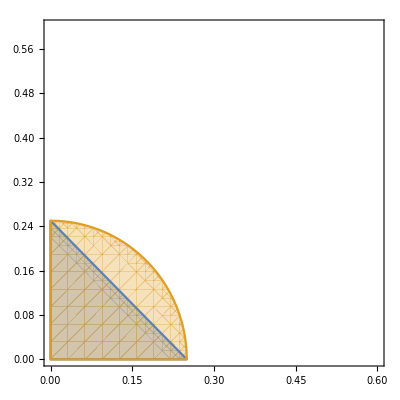

```mathematica
RegionPlot[ {α+β≤ 1/4,√(α^2+β^2)<1/4},{α,0,0.6},{β,0,0.6}]
```

```mathematica
Manipulate[
Show[
RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"bound",{0.1,0.4}],{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Green]],
RegionPlot[Callout[α+β≤ 1/4,"abs. convergence",{0.3,0.15}],{α,0,0.6},{β,0,0.6}],
RegionPlot[(-β^2 x^2+(4α^2+β^2) x≤1/8 ),{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.3],Orange],FrameLabel->{"α","β"}]
]
,{x,0.5,1}]
```

```mathematica
Export[NotebookDirectory[]<>"img/region-ext1.pdf",%521];
```

```mathematica
SystemOpen["/Users/jiaan/Desktop/DD-threshold/img/region-ext1.pdf"]
```

```mathematica
(* with noise: theory *)
```

```mathematica
(* first, what's the maximum effective β with noise? *)
```

```mathematica
{B[0],B[1],B[2],B[3]}={σ[1],σ[0],0σ[0],0σ[2]}
```

{{{0,1/(√2)},{1/(√2),0}},{{1/(√2),0},{0,1/(√2)}},{{0,0},{0,0}},{{0,0},{0,0}}}

```mathematica
getNoiseβ[β_?NumericQ,θ1_?NumericQ,θ2_?NumericQ,θ3_?NumericQ]:=Norm2SB[ⅈ MatrixLog[MatrixExp[-ⅈ ΩSB[β]].KroneckerProduct[MatrixExp[-ⅈ 1/2{θ1,θ2,θ3}.{X,Y,Z}],Id]]];
getNoiseβ[0.1,0.1,0,0]
```

0.2

```mathematica
NMaximize[{getNoiseβ[0.1,n1,n2,n3],n1^2+n2^2+n3^2==0.1^2},{n1,n2,n3}]
```

{0.2,{n1→0.1,n2→4.48955×10^-8,n3→-6.70745×10^-9}}

```mathematica
(* The crude model: just change β -> β+θ, and use second order Magnus *)
```

```mathematica
Manipulate[
Show[
RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"noiseless",{0.3,0.6}],{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Orange]],
RegionPlot[(α<(β+θ)/2&&√2(4α^2+(β+θ)^2)≤ β)||(α≥(β+θ)/2&&4 √2 α(β+θ)≤β),{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Green]]],{θ,0,1/(4 √2)}]
```

```mathematica
plotbound[θ_,n_:1]:=RegionPlot[Evaluate[{
Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n/2)α^(n-1)))||(α≥β/2^n&&α≤ 1/2^(n+3/2)),"noiseless",{0.3,0.6}],
Callout[(α<(β+θ)/2^n&&(4^n α^2+(β+θ)^2)/2≤ β/(2^(n^2+n/2)α^(n-1)))||(α≥(β+θ)/2^n&&2^(n+3/2)α(β+θ)≤β),"with noise",{0.3,0.3}]}]
,{α,0,1},{β,0,1},PlotStyle->{Directive[Opacity[0.5],Orange],Directive[Opacity[0.5],Green]},FrameLabel->{"α","β"},Epilog->Inset[Framed[Text["θ= "<>ToString[θ]],Background->LightYellow],{0.9,0.9}]]
```

```mathematica
plotbound2[θ_,n_:1]:=RegionPlot[Evaluate[{
Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n/2)α^(n-1)))||(α≥β/2^n&&α≤ 1/2^(n+3/2)),"noiseless",{0.3,0.6}],
Callout[(α<(β+θ)/2^n&&(4^n α^2+(β+θ)^2)/2≤ β/(2^(n^2+n/2)α^(n-1)))||(α≥(β+θ)/2^n&&2^(n+3/2)α(β+θ)≤β),"with noise",{0.3,0.3}]}]
,{α,0,1},{β,0,1},PlotStyle->{Directive[Opacity[0.5],Orange],Directive[Opacity[0.5],Green]},FrameLabel->{"α","β"},Epilog->Inset[Framed[TextGrid[{{"n= "<>ToString[n]},{"θ= "<>ToString[θ]}}],Background->LightYellow],{0.9,0.9}]]
```

```mathematica
Manipulate[plotbound2[θ,2],{θ,0,1}]
```

```mathematica
1./(4 √2)
```

0.176777

```mathematica
Module[{n=2},RegionPlot[{Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n/2)α^(n-1)))||(α≥ β/2^n>0&&α≤ 1/2^(n+3/2)),"noise removal",{0.2,0.4}],
Callout[α^2+β^2≤ 1/16^n,"abs. converge",{0.3,0.15}]},{α,0,1},{β,0,1},FrameLabel->{"α","β"}]]
Export[NotebookDirectory[]<>"img/region2.pdf",%]
```

```mathematica
GraphicsGrid[{{plotbound2[0.1,2],plotbound2[0.2,2]},{plotbound2[0.1,3],plotbound2[0.2,3]}}]
Export[NotebookDirectory[]<>"img/noise-bound2.pdf",%];
```

-Graphics-

```mathematica
Manipulate[
Show[
RegionPlot[Callout[(0<α<β/2&&4α^2+β^2-β/√2≤ 0)||(α≥ β/2>0&&α≤ √2/8),"noiseless",{0.3,0.6}],{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Orange]],
RegionPlot[(α<(β+θ)/2&&√2(4α^2+(β+θ)^2)≤ β)||(α≥(β+θ)/2&&4 √2 α(β+θ)≤β),{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Green]]],{θ,0,1/(4 √2)}]
```

```mathematica
(* α=0 *)
```

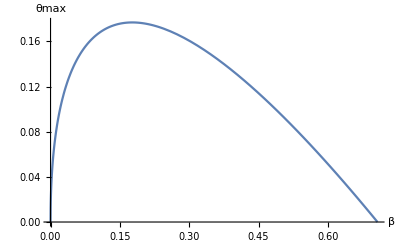

```mathematica
Plot[(√β)/2^(1/4)-β,{β,0,1/(√2)},AxesLabel->{"β","θmax"}]
Export["
```

```mathematica
Maximize[(√β)/2^(1/4)-β,β]
```

{1/(4 √2),{β→1/(4 √2)}}

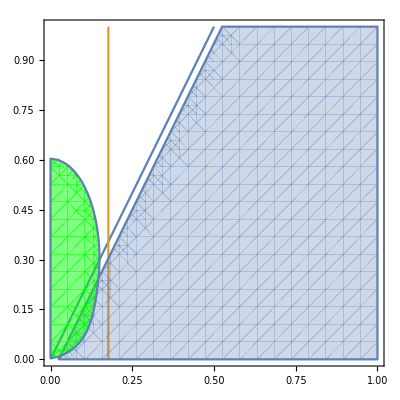

```mathematica
Module[{θ=0.05},Show[
ContourPlot[{2α-β==0,β/(4 √2 α)-β==0},{α,0,1},{β,0,1}],
RegionPlot[{2α-β>θ},{α,0,1},{β,0,1}],
RegionPlot[(2α<β+θ&&√2(4α^2+(β+θ)^2)≤ β)||(2α≥β+θ&&4 √2 α(β+θ)≤β),{α,0,1},{β,0,1},PlotStyle->Directive[Opacity[0.5],Green]]
]]
```

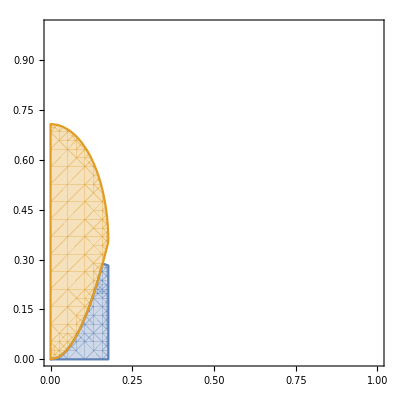

```mathematica
Show[RegionPlot[{β<8 √2 α^2&&α<=(√2)/8,β>8 √2 α^2&&√(β/(√2)-4 α^2)-β>0},{α,0,1},{β,0,1}]]
```

```mathematica
(* 3-D plot: α,β vs θmax *)
```

```mathematica
θmax[α_,β_]:=Piecewise[{{β/(4 √2 α)-β,β<8 √2 α^2&&α≤(√2)/8},{√(β/(√2)-4 α^2)-β,β≥ 8 √2 α^2&&√(β/(√2)-4 α^2)-β>0}},0]
```

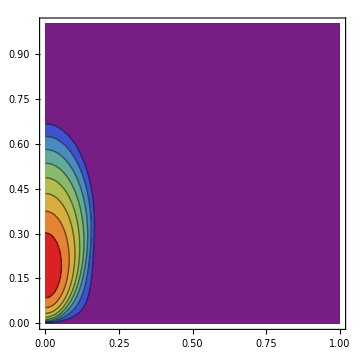

/Users/jiaan/Desktop/DD-threshold/img/threshold.pdf

```mathematica
θmaxdata=Table[{α,β,θmax[α,β]},{α,0,1,0.01},{β,0,1,0.01}];
ListContourPlot[Flatten[θmaxdata,1],ColorFunction->"Rainbow",PlotRange->All,ImageSize->Medium]
Export[NotebookDirectory[]<>"img/threshold.pdf",%]
```

```mathematica
Export["~/Desktop/threshold.png",pic]
```

~/Desktop/threshold.png

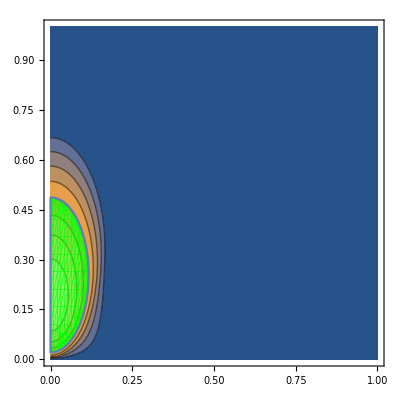

```mathematica
Module[{θ=0.1},Show[
ListContourPlot[Flatten[θmaxdata,1]],
RegionPlot[(2α<β+θ&&√2(4α^2+(β+θ)^2)≤ β)||(2α≥β+θ&&4 √2 α(β+θ)≤β),{α,0,0.2},{β,0,1},PlotStyle->Directive[Opacity[0.5],Green]]
]]
```

```mathematica
(* with noise: simulation *)
```

```mathematica
{B[0],B[1],B[2],B[3]}={σ[1],√x σ[2],0 IdentityMatrix[2],√(1-x)σ[2]}/.x->0.7;
Norm2/@{B[0],Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}]}
```

{1,1.}

```mathematica
Module[{α=0.1,β=0.1,θ=0.1},
Ke=θ*Normalize[RandomReal[{-1,1},{3}]].{σ[1],σ[2],σ[3]};
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
Uef=(KroneckerProduct[MatrixExp[-ⅈ Ke],Id]).Uf;
Ωef=Chop[ⅈ MatrixLog[Uef]];
Udde=PDD[Uef];
Ωdde=Chop[ⅈ MatrixLog[Udde]];
{Norm2SB[Ω0],Norm2[Ke],Norm2SB[Ωef],Norm2SB[Ωdde]}
]
```

{0.1,0.1,0.10576,0.00110267}

```mathematica
(* noise maximization *)
```

```mathematica
(* the error phase for the effective noise *)
```

```mathematica
getErrPh[Uf_,θ_,n1_?NumericQ,n2_?NumericQ,n3_?NumericQ]:=
Module[{K,Uef},
K=θ*{n1,n2,n3}.{σ[1],σ[2],σ[3]};
Uef=KroneckerProduct[MatrixExp[-ⅈ K],Id].Uf;
Norm2SB[ⅈ MatrixLog[Uef]]
]
```

```mathematica
Module[{α=0.1,β=0.1,θ=0.1},
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
NMaximize[{getErrPh[Uf,θ,n1,n2,n3]},{n1,n2,n3}∈Sphere[]][[1]]
]
```

0.173205

```mathematica
getErrPhdd[Uf_,θ_,n1_?NumericQ,n2_?NumericQ,n3_?NumericQ]:=
Module[{K,Udd},
K=θ*{n1,n2,n3}.{σ[1],σ[2],σ[3]};
Udd=PDD[KroneckerProduct[MatrixExp[-ⅈ K],Id].Uf];
Norm2SB[ⅈ MatrixLog[Udd]]
]
```

```mathematica
AbsoluteTiming[
dataβnvsθ=ParallelTable[
Module[{α=0.1,β=0.1},
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
{θ,NMaximize[{getErrPh[Uf,θ,n1,n2,n3]},{n1,n2,n3}∈Sphere[]][[1]]}
],{θ,0,0.5,0.05}];
]
```

{8.45118,Null}

```mathematica
Fit[dataβnvsθ,{1,x},x]
```

0.0592909+1.27967 x

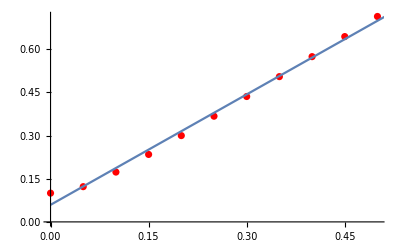

```mathematica
Show[ListPlot[dataβnvsθ,PlotStyle->Red],Plot[0.05929090706257133+1.2796705943380704 x,{x,0,1}]]
```

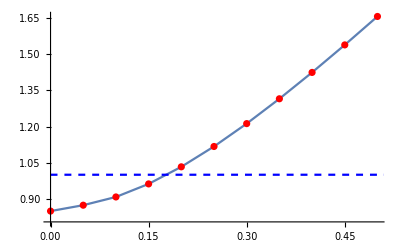

```mathematica
Module[{α=0,β=1},
dataβnvsθ=ParallelTable[
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
{θ,NMaximize[{getErrPhdd[Uf,θ,n1,n2,n3]},{n1,n2,n3}∈Sphere[]][[1]]}
,{θ,0,0.5,0.05}];
Show[ListPlot[dataβnvsθ,Joined->True,Mesh->All,MeshStyle->Red],Plot[β,{x,0,1},PlotStyle->{Dashed,Blue}]]]
```

```mathematica
getMaxErrPh[α_?NumericQ,β_?NumericQ,θ_?NumericQ]:=Module[{Ω0,Uf},
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
NMaximize[{getErrPhdd[Uf,θ,n1,n2,n3]},{n1,n2,n3}∈Sphere[]][[1]]
]
```

```mathematica
FindRoot[getMaxErrPh[0,0.1,θ]-0.1,{θ,0,0.1}]
```

{θ→0.195204}

```mathematica
AbsoluteTiming[
dataθmaxvsβ=
Module[{α=0},
ParallelTable[
{β,θ/.FindRoot[getMaxErrPh[α,β,θ]-β,{θ,0,0.1}]},{β,0,1,0.05}]
]]
```

{188.376,{{0.,0.},{0.05,0.14766},{0.1,0.195204},{0.15,0.223788},{0.2,0.24229},{0.25,0.254453},{0.3,0.262298},{0.35,0.26703},{0.4,0.269411},{0.45,0.269922},{0.5,0.268869},{0.55,0.266438},{0.6,0.262729},{0.65,0.257772},{0.7,0.251545},{0.75,0.243972},{0.8,0.234922},{0.85,0.224192},{0.9,0.211486},{0.95,0.196363},{1.,0.17813}}}

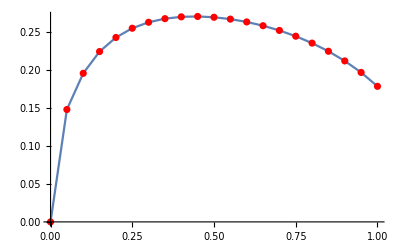

```mathematica
ListPlot[dataθmaxvsβ,Joined->True,Mesh->All,MeshStyle->Red]
```

```mathematica
(* with random bath operators *)
```

```mathematica
B[0]=Normalize[RandomReal[{-1,1},3]].{σ[1],σ[2],σ[3]};
{B[1],B[2],B[3]}=ArrayReshape[Normalize[RandomReal[{-1,1},12]],{3,4}].Table[σ[i],{i,0,3}];
Norm2/@{KroneckerProduct[σ[0],B[0]],Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}]}
```

{1.,1.}

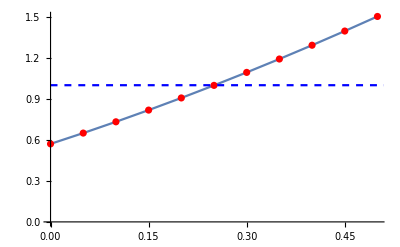

```mathematica
Module[{α=0,β=1},
dataβnvsθ2=ParallelTable[
Ω0=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
Uf=MatrixExp[-ⅈ Ω0];
{θ,NMaximize[{getErrPhdd[Uf,θ,n1,n2,n3]},{n1,n2,n3}∈Sphere[]][[1]]}
,{θ,0,0.5,0.05}];
Show[ListPlot[dataβnvsθ2,Joined->True,Mesh->All,MeshStyle->Red],Plot[β,{x,0,1},PlotStyle->{Dashed,Blue}]]]
```

```mathematica
AbsoluteTiming[
dataθmaxvsβ2=
Module[{α=0},
ParallelTable[
{β,θ/.FindRoot[getMaxErrPh[α,β,θ]-β,{θ,0,0.1}]},{β,0,1,0.05}]
]]
```

{184.347,{{0.,0.},{0.05,0.136845},{0.1,0.180199},{0.15,0.20793},{0.2,0.227556},{0.25,0.242015},{0.3,0.252821},{0.35,0.260874},{0.4,0.26676},{0.45,0.270882},{0.5,0.273534},{0.55,0.274931},{0.6,0.275242},{0.65,0.274598},{0.7,0.273105},{0.75,0.270853},{0.8,0.267919},{0.85,0.264372},{0.9,0.260275},{0.95,0.255688},{1.,0.250668}}}

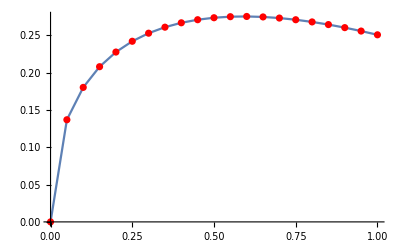

```mathematica
ListPlot[dataθmaxvsβ2,Joined->True,Mesh->All,MeshStyle->Red]
```

```mathematica
(* channel distance measure *)
```

```mathematica
chid=IdentityMatrix[4];
unvec2[p_]:=Simplify[p.Flatten[Table[KroneckerProduct[σ[i],σ[j]],{i,0,3},{j,0,3}],1]];
trNorm[X_]:=Total[SingularValueList[X]] ;(* Trace norm for states *)
TrNorm[X_]:=NMaximize[Norm[Rest[X.{1,p1,p2,p3}]],{p1,p2,p3}∈Sphere[]][[1]] ;(* induced trace norm *)
chtrNorm2[channel_,θ1_?NumericQ,θ2_?NumericQ,θ3_?NumericQ,ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ]:=Module[{ψ},
ψ=KroneckerProduct[channel,IdentityMatrix[4]].{1/2,Cos[θ1]^2 Cos[θ2] Cos[ϕ1] Sin[θ2]+Cos[θ3] Cos[ϕ2-ϕ3] Sin[θ1]^2 Sin[θ3],Cos[θ1]^2 Cos[θ2] Sin[θ2] Sin[ϕ1]-Cos[θ3] Sin[θ1]^2 Sin[θ3] Sin[ϕ2-ϕ3],1/2 (Cos[θ1]^2 Cos[2 θ2]+Cos[2 θ3] Sin[θ1]^2),Cos[θ1] Sin[θ1] (Cos[θ2] Cos[θ3] Cos[ϕ2]+Cos[ϕ1-ϕ3] Sin[θ2] Sin[θ3]),Cos[θ1] Sin[θ1] (Cos[θ3] Cos[ϕ1-ϕ2] Sin[θ2]+Cos[θ2] Cos[ϕ3] Sin[θ3]),Cos[θ1] Sin[θ1] (Cos[θ3] Sin[θ2] Sin[ϕ1-ϕ2]+Cos[θ2] Sin[θ3] Sin[ϕ3]),Cos[θ1] Sin[θ1] (Cos[θ2] Cos[θ3] Cos[ϕ2]-Cos[ϕ1-ϕ3] Sin[θ2] Sin[θ3]),Cos[θ1] Sin[θ1] (Cos[θ2] Cos[θ3] Sin[ϕ2]-Sin[θ2] Sin[θ3] Sin[ϕ1-ϕ3]),Cos[θ1] Sin[θ1] (-Cos[θ3] Sin[θ2] Sin[ϕ1-ϕ2]+Cos[θ2] Sin[θ3] Sin[ϕ3]),Cos[θ1] Sin[θ1] (Cos[θ3] Cos[ϕ1-ϕ2] Sin[θ2]-Cos[θ2] Cos[ϕ3] Sin[θ3]),Cos[θ1] Sin[θ1] (Cos[θ2] Cos[θ3] Sin[ϕ2]+Sin[θ2] Sin[θ3] Sin[ϕ1-ϕ3]),1/2 Cos[2 θ1],Cos[θ1]^2 Cos[θ2] Cos[ϕ1] Sin[θ2]-Cos[θ3] Cos[ϕ2-ϕ3] Sin[θ1]^2 Sin[θ3],Cos[θ1]^2 Cos[θ2] Sin[θ2] Sin[ϕ1]+Cos[θ3] Sin[θ1]^2 Sin[θ3] Sin[ϕ2-ϕ3],1/2 (Cos[θ1]^2 Cos[2 θ2]-Cos[2 θ3] Sin[θ1]^2)};
trNorm[unvec2[ψ]]];
DiamondNorm[X_]:=NMaximize[{chtrNorm2[X,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3],
0≤ θ1≤ π/2&&0≤ θ2≤ π/2&&0≤ θ3≤ π/2&&0≤ ϕ1≤2π&&0≤ ϕ2≤2π&&0≤ ϕ3≤2π},{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3}][[1]]
```

```mathematica
ρB={{1-t,0},{0,t}}/.t->0;
ρB//MatrixForm
```

(1 | 0
0 | 0)

```mathematica
Uf=MatrixExp[-ⅈ Ω[0.1,0.1]];MatrixForm[Uf]
```

(0.997502+0. ⅈ | 0.-0.0499167 ⅈ | 0.-0.0499167 ⅈ | -0.00249792+0. ⅈ
0.-0.0499167 ⅈ | 0.997502+0. ⅈ | -0.00249792+0. ⅈ | 0.-0.0499167 ⅈ
0.-0.0499167 ⅈ | -0.00249792+0. ⅈ | 0.997502+0. ⅈ | 0.-0.0499167 ⅈ
-0.00249792+0. ⅈ | 0.-0.0499167 ⅈ | 0.-0.0499167 ⅈ | 0.997502+0. ⅈ)

```mathematica
B[0]=Normalize[RandomReal[{-1,1},3]].{σ[1],σ[2],σ[3]};
{B[1],B[2],B[3]}=ArrayReshape[Normalize[RandomReal[{-1,1},12]],{3,4}].Table[σ[i],{i,0,3}];
```

```mathematica
{B[0],B[1],B[2],B[3]}=Evaluate[{σ[1],√x σ[2],0 IdentityMatrix[2],√(1-x)σ[2]}/.x->0.5];
```

```mathematica
(* convert unitary operator into a channel *)
```

```mathematica
AbsoluteTiming[disαβ=ParallelTable[
chf=U2Ch[MatrixExp[-ⅈ Ω[α,β]],ρB];
{α,β,NMaximize[Norm[Rest[(chf-IdentityMatrix[4]).{1,p1,p2,p3}]],{p1,p2,p3}∈Sphere[]][[1]]}
,{α,0.0,0.9,0.1},{β,0.0,0.9,0.1}];]
```

{27.2908,Null}

```mathematica
Norm[Rest[(chf-IdentityMatrix[4]).{1,p1,p2,p3}]]//MatrixForm
```

√(0.0000249584 Abs[p2]^2+Abs[0.00249792 p1-0.00249792 p3]^2+Abs[-0.00249792 p1+0.00249792 p3]^2)

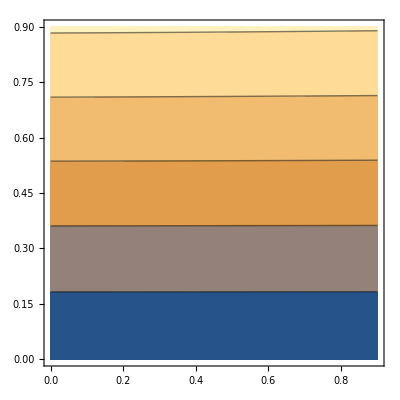

```mathematica
ListContourPlot[Flatten[disαβ,1]]
```

```mathematica
{B[0],B[1],B[2],B[3]}=Evaluate[{σ[1],√x σ[2],0 IdentityMatrix[2],√(1-x)σ[2]}/.x->0.5];
```

```mathematica
disdiff=ParallelTable[
Uf=MatrixExp[-ⅈ Ω[α,β]];
chfu=U2ChUni[Uf,ρB];chddu=U2ChUni[PDD[Uf],ρB];
{α,β,Norm[chfu-IdentityMatrix[3]]-Norm[chddu-IdentityMatrix[3]]}
,{α,0,1,0.01},{β,0.,1,0.01}];
```

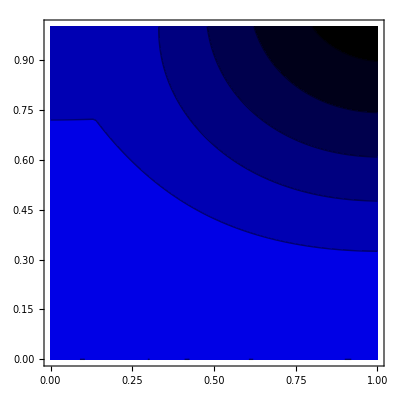

```mathematica
ListContourPlot[Flatten[disdiff,1],ColorFunction->colorfun1,ColorFunctionScaling->False]
```

```mathematica
Module[{α=0.,β=0.1},
Uf=MatrixExp[-ⅈ Ω[α,β]];
chf=U2Ch[Uf,ρB]//Chop;
Udd=PDD[Uf];
Ωdd=ⅈ MatrixLog[Udd];
chdd=U2Ch[Udd,ρB]//Chop;
{NormDis[chf],TrNormDis[chf],DiamondNormDis[chf],NormDis[chdd],TrNormDis[chdd],DiamondNormDis[chdd]}
]
```

{0.00499583,0.00499583,0.00499583,0.00996684,0.00996684,0.00996684}

```mathematica
B[0]=Normalize[RandomReal[{-1,1},3]].{σ[1],σ[2],σ[3]};
{B[1],B[2],B[3]}=ArrayReshape[Normalize[RandomReal[{-1,1},12]],{3,4}].Table[σ[i],{i,0,3}];
disdiff2=ParallelTable[
Uf=MatrixExp[-ⅈ Ω[α,β]];
chfu=U2ChUni[Uf,ρB];chddu=U2ChUni[PDD[Uf],ρB];
{α,β,Norm[chfu-IdentityMatrix[3]]-Norm[chddu-IdentityMatrix[3]]}
,{α,0,1,0.01},{β,0.,1,0.01}];
```

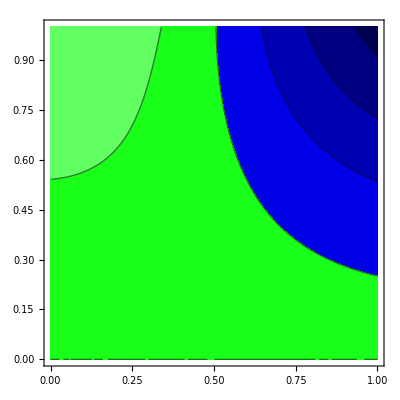

```mathematica
ListContourPlot[Flatten[disdiff2,1],ColorFunction->colorfun1,ColorFunctionScaling->False]
```

```mathematica
(* introduce noise *) 
Module[{α=0.1,β=0.1,θ=0.1},
Uf=MatrixExp[-ⅈ Ω[α,β]];
Ke=θ*Normalize[RandomReal[{-1,1},{3}]].{σ[1],σ[2],σ[3]};
Uef=KroneckerProduct[MatrixExp[-ⅈ Ke],Id].Uf;
Udde=PDD[Uef];
{Norm[U2ChUni[Uf,ρB]-IdentityMatrix[3]],Norm[U2ChUni[Udde,ρB]-IdentityMatrix[3]]}
]
```

{0.00499167,0.0106886}

```mathematica
(* noise maximization *)
```

```mathematica
getDis[α_,β_]:=Norm[U2ChUni[MatrixExp[-ⅈ Ω[α,β]],ρB]-IdentityMatrix[3]]
```

```mathematica
getNoiseDisDD[Uf_,n1_?NumericQ,n2_?NumericQ,n3_?NumericQ]:=
Module[{Udd=PDD[KroneckerProduct[MatrixExp[-ⅈ 1/2{n1,n2,n3}.{X,Y,Z}],Id].Uf]},
Norm[U2ChUni[Udd,ρB]-IdentityMatrix[3]]
]
```

```mathematica
ρB={{1/2,0},{0,1/2}}
```

{{1/2,0},{0,1/2}}

```mathematica
Udd=MatrixExp[-ⅈ Ω[0.1,0.1]];
```

```mathematica
U2Ch[Udd,ρB]//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 0.995981 | 0.0128115 | 0.0176815
0 | -0.0126272 | 0.998684 | 0.0104414
0 | -0.0180127 | -0.00907383 | 0.995352)

```mathematica
U2ChUni[Udd,ρB]-IdentityMatrix[3]//Chop//MatrixForm
```

(-0.0000499164 | 0 | -0.00996659
0 | -2.48753×10^-7 | 0
0.00996659 | 0 | -0.0000496677)

```mathematica
getMaxNoiseDis[α_?NumericQ,β_?NumericQ,θ_?NumericQ]:=NMaximize[{getNoiseDisDD[MatrixExp[-ⅈ Ω[α,β]],n1,n2,n3],n1^2+n2^2+n3^2==θ^2},{n1,n2,n3}][[1]]
```

```mathematica
AbsoluteTiming[getMaxNoiseDis[0.1,0.1,0.1]]
```

{2.85891,0.0195137}

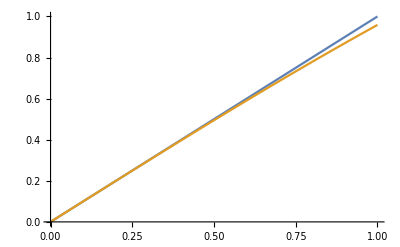

```mathematica
Plot[{β,Evaluate[getDis[0,β]]},{β,0,1}]
```

```mathematica
AbsoluteTiming[FindRoot[getMaxNoiseDis[0,0.1,θ]-0.1,{θ,0,0.1}]]
```

{56.988,{θ→0.251268}}

```mathematica
AbsoluteTiming[
dataMaxNoiseDisvsβ=
Module[{α=0},
ParallelTable[
{β,θ/.FindRoot[getMaxNoiseDis[α,β,θ]-getDis[α,β],{θ,0,0.1}]},{β,0.05,1,0.05}]
]]
```

{564.463,{{0.05,0.190221},{0.1,0.251202},{0.15,0.291834},{0.2,0.322311},{0.25,0.346543},{0.3,0.366517},{0.35,0.383397},{0.4,0.397936},{0.45,0.410651},{0.5,0.421913},{0.55,0.431999},{0.6,0.441121},{0.65,0.449448},{0.7,0.457111},{0.75,0.46422},{0.8,0.470863},{0.85,0.477116},{0.9,0.483042},{0.95,0.488693},{1.,0.494117}}}

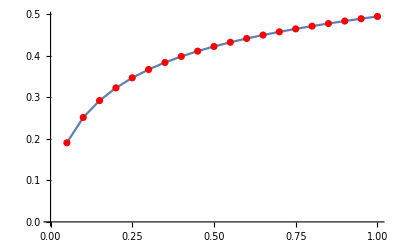

```mathematica
ListPlot[dataMaxNoiseDisvsβ,Joined->True,Mesh->All,MeshStyle->Red]
```

```mathematica
AbsoluteTiming[dataNoiseDisvsθ=ParallelTable[{θ,getMaxNoiseDis[0,2,θ]},{θ,0,0.5,0.05}]]
```

{17.6251,{{0.,2.49451×10^-8},{0.05,0.0959177},{0.1,0.192024},{0.15,0.288471},{0.2,0.385349},{0.25,0.482667},{0.3,0.580345},{0.35,0.678217},{0.4,0.776035},{0.45,0.873482},{0.5,0.970176}}}

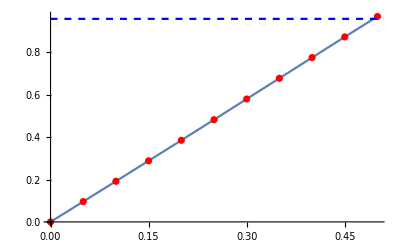

```mathematica
Show[ListPlot[dataNoiseDisvsθ,Joined->True,Mesh->All,MeshStyle->Red],Plot[getDis[0,1],{x,0,1},PlotStyle->{Dashed,Blue}]]
```

```mathematica
(* using fidelity measure *)
```

```mathematica
dataRandInf=Table[
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/(√2)(σ[0]+ps.{σ[1],σ[2],σ[3]});
Table[Module[{Ht,U0},
Ht=0.1*KroneckerProduct[σ[0],B[0]]+β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
ρT=U0.KroneckerProduct[ρS,ρE].U0†;
ρST=Map[Tr,Partition[ρT,{2,2}],{2}];
{β,Re[1-Tr[ρS.ρST]]}],{β,0,0.25,0.025}],{i,1,200}];
```

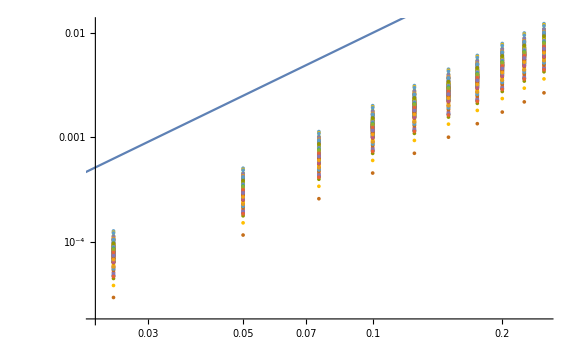

```mathematica
Show[ListLogLogPlot[dataRandInf,ImageSize->Large],LogLogPlot[β^2,{β,0,0.25}]]
```

```mathematica
cm[A_,B_]:=A.B-B.A;
am[A_,B_]:=A.B+B.A;
```

```mathematica
(* The difference in fidelity between free and DD *)
fidDiff[α_,β_]:=Module[{Ht,U0,UDD,ρST,ρSTDD},Ht=α*KroneckerProduct[σ[0],B[0]]+β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
UDD=KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
ρST=Map[Tr,Partition[U0.KroneckerProduct[ρS,ρE].U0†,{2,2}],{2}];
ρSTDD=Map[Tr,Partition[UDD.KroneckerProduct[ρS,ρE].UDD†,{2,2}],{2}];
Re[Tr[ρS.(ρSTDD-ρST)]]]
```

```mathematica
ρS
```

{{0.583552+0. ⅈ,0.360312-0.336444 ⅈ},{0.360312+0.336444 ⅈ,0.416448+0. ⅈ}}

```mathematica
fidDiff[0.1,0.1]
```

-0.993014

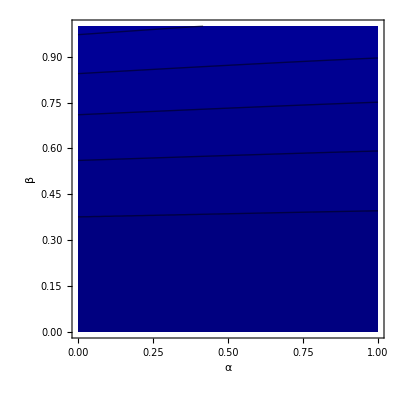

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
ρE={{0,0},{0,1}};
{B[0],B[1],B[2],B[3]}=Table[
Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]}/√2,{i,1,4}];

ContourPlot[fidDiff[α,β],{α,0,1},{β,0,1},FrameLabel->{"α","β"},ColorFunction->(If[#<0,Darker[Blue,Abs[#]],Darker[Green,#]]&),ColorFunctionScaling->False]
```

```mathematica
dataBound={};
Module[{α,α0,β},
For[β=0.01,β<0.5,β+=0.01,
intp=Interpolation[Table[{α,fidDiff[α,β]},{α,0.0,0.4,0.01}]];
α0=x/.FindRoot[intp[x]==0,{x,0.4,0.3}];
If[α0<0.001,Break[]];
AppendTo[dataBound,{α0,β}];]
];
```

InterpolatingFunction::dmval: Input value {0.450963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.444098} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
```

```mathematica
getbound[f_]:=Module[{x=0,αstop=1,βstop=1,res=0.001,inc=0.01,s,data},
data={};
Do[
If[f[res,β]<0,αstop=x;βstop=β-inc;Break[]];
x=0;s=0.1;
While[x+s≤1&&s>res,
If[f[x+s,β]>0,
x=x+s;Continue[],
s=s/2];
];

If[x<1,AppendTo[data,{x,β}];];
,{β,inc,1,inc}
];

If[βstop<1&&αstop>inc,
Do[
x=βstop;s=inc;

While[x+s≤1&&s>res,
If[f[α,x+s]>0,
x=x+s;Continue[],
s=s/2];
];

If[x<1,AppendTo[data,{α,x}];];
,{α,αstop,inc,-inc}
];
];
data
]
```

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
```

```mathematica
{B[0],B[1],B[2],B[3]}=Table[
Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]}/√2,{i,1,4}];
```

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
```

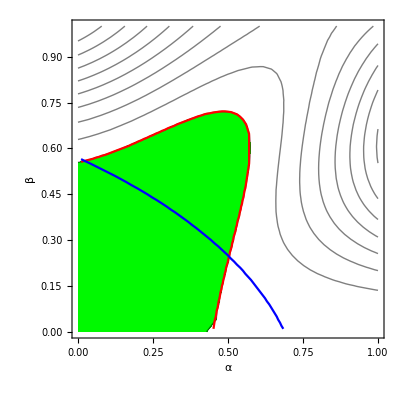

```mathematica
dataBound=getbound[fidDiff];
dataBoundapp=getbound[fidDiffMagnus];
Show[
ContourPlot[fidDiff[α,β],{α,0,1},{β,0,1},FrameLabel->{"α","β"},ColorFunction->(If[#<0,Transparent,Darker[Green,#]]&),ColorFunctionScaling->False],ListPlot[{dataBound,dataBoundapp},Joined->True,PlotRange->{{0,1},{0,1}},PlotStyle->{Red,Blue},AspectRatio->1]]
```

```mathematica
AbsoluteTiming[dataBounds=Table[
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
getbound[fidDiff],{i,1,100}];]
```

{16.9451,Null}

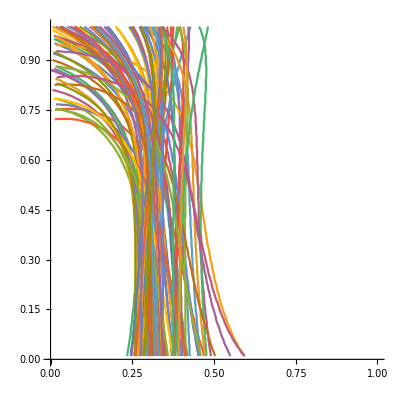

```mathematica
ListPlot[dataBounds,PlotRange->{{0,1},{0,1}},AspectRatio->1,Joined->True]
```

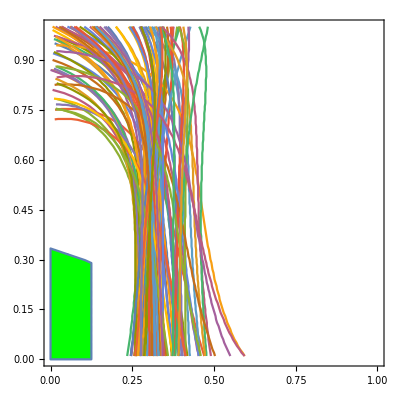

```mathematica
Show[RegionPlot[0<α<1/8&&0<β<3/8&&α+3β<1,{α,0,1},{β,0,1},PlotStyle->Green],ListPlot[dataBounds,PlotRange->{{0,1},{0,1}},AspectRatio->1,Joined->True]]
```

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
ρE={{0,0},{0,1}};
{B[0],B[1],B[2],B[3]}=Table[
Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]}/√2,{i,1,4}];
```

```mathematica
ps=Normalize[RandomReal[{0,1},3]];
ρS=1/2 σ[0]+1/2 ps.{σ[1],σ[2],σ[3]};
dataBound={};
Module[{α,res=0.01,s,f=fidDiff},
Do[Do[
If[f[α,β]< 0,
AppendTo[dataBound,{α,β-res/2}];s=β;Break[]],{β,0,1,res}];
If[s==res,Break[]],{α,0,1,res}
]]
dataBoundapp={};
Module[{α,res=0.01,s,f=fidDiff},
Do[Do[
If[f[α,β]< 0,
AppendTo[dataBoundapp,{α,β-res/2}];s=β;Break[]],{β,0,0.5,res}];
If[s==res,Break[]],{α,0,0.5,res}
]]
ListPlot[{dataBound,dataBoundapp},Joined->True,PlotRange->{{0,0.5},{0,0.5}},AspectRatio->1]
```

```mathematica
Norm/@{B[0],B[1],B[2],B[3]}
```

{0.993463,0.999868,0.916204,0.95742}

```mathematica
(* Noise removal condition *)
```

```mathematica
Flatten[Array[Subscript[b, #1,#2]&,{4,4},0]]
```

{b_(0,0),b_(0,1),b_(0,2),b_(0,3),b_(1,0),b_(1,1),b_(1,2),b_(1,3),b_(2,0),b_(2,1),b_(2,2),b_(2,3),b_(3,0),b_(3,1),b_(3,2),b_(3,3)}

```mathematica
ρE={{1,0},{0,0}};
```

```mathematica
{B[0],B[1],B[2],B[3]}=Array[Subscript[b, #1,#2]&,{4,4},0].{σ[0],σ[1],σ[2],σ[3]}/√2;
BDD[1]=-4ⅈ α β cm[B[0],B[1]]//Simplify;
BDD[2]=-2ⅈ α β  cm[B[0],B[2]]+2 β^2 am[B[1],B[3]]//Simplify;
BDD[3]=0IdentityMatrix[2];
```

```mathematica
BB0=Expand[2Table[Tr[B[i].B[j].ρE],{i,1,3},{j,1,3}]]/.{Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2->1,Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2->1,Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2->1};
```

```mathematica
M0=Tr[BB0]*IdentityMatrix[3]-ComplexExpand[Re[BB0]];
t0=ComplexExpand[-2{Im[BB0][[2,3]],Im[BB0][[3,1]],Im[BB0][[1,2]]}];
```

```mathematica
t0
```

{2 b_(2,2) b_(3,1)-2 b_(2,1) b_(3,2),-2 b_(1,2) b_(3,1)+2 b_(1,1) b_(3,2),2 b_(1,2) b_(2,1)-2 b_(1,1) b_(2,2)}

```mathematica
M0
```

{{2+2 b_(2,0) b_(2,3)+2 b_(3,0) b_(3,3),-b_(1,0) b_(2,0)-b_(1,3) b_(2,0)-b_(1,1) b_(2,1)-b_(1,2) b_(2,2)-b_(1,0) b_(2,3)-b_(1,3) b_(2,3),-b_(1,0) b_(3,0)-b_(1,3) b_(3,0)-b_(1,1) b_(3,1)-b_(1,2) b_(3,2)-b_(1,0) b_(3,3)-b_(1,3) b_(3,3)},{-b_(1,0) b_(2,0)-b_(1,3) b_(2,0)-b_(1,1) b_(2,1)-b_(1,2) b_(2,2)-b_(1,0) b_(2,3)-b_(1,3) b_(2,3),2+2 b_(1,0) b_(1,3)+2 b_(3,0) b_(3,3),-b_(2,0) b_(3,0)-b_(2,3) b_(3,0)-b_(2,1) b_(3,1)-b_(2,2) b_(3,2)-b_(2,0) b_(3,3)-b_(2,3) b_(3,3)},{-b_(1,0) b_(3,0)-b_(1,3) b_(3,0)-b_(1,1) b_(3,1)-b_(1,2) b_(3,2)-b_(1,0) b_(3,3)-b_(1,3) b_(3,3),-b_(2,0) b_(3,0)-b_(2,3) b_(3,0)-b_(2,1) b_(3,1)-b_(2,2) b_(3,2)-b_(2,0) b_(3,3)-b_(2,3) b_(3,3),2+2 b_(1,0) b_(1,3)+2 b_(2,0) b_(2,3)}}

```mathematica
NMinimize[{{p1,p2,p3}.t0+{p1,p2,p3}.M0.{p1,p2,p3},
Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1&&Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&p1^2+p2^2+p3^2==1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],p1,p2,p3}]
```

{-6.45872×10^-13,{b_(1,0)→0.899989,b_(1,1)→0.364566,b_(1,2)→0.125918,b_(1,3)→-0.203118,b_(2,0)→0.802005,b_(2,1)→-0.269149,b_(2,2)→-0.10142,b_(2,3)→-0.523509,b_(3,0)→0.80536,b_(3,1)→0.00749853,b_(3,2)→0.550498,b_(3,3)→-0.219751,p1→-0.732079,p2→-0.292566,p3→-0.615196}}

```mathematica
BBDD=Collect[2 β^-2 Table[Tr[BDD[i].BDD[j].ρE],{i,1,3},{j,1,3}],{α,β},Simplify];
```

```mathematica
MDD=Simplify[Collect[ComplexExpand[Tr[BBDD]IdentityMatrix[3]-Re[BBDD]],{α,β},Simplify]/.{Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2-> 1,Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2-> 1,Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2-> 1}];
tDD=ComplexExpand[-2{Im[BBDD][[2,3]],Im[BBDD][[3,1]],Im[BBDD][[1,2]]}];
```

```mathematica
BBDD/.α->0//MatrixForm
```

(0 | 0 | 0
0 | 8 β^2 (b_(1,1)^2 b_(3,0)^2+b_(1,2)^2 b_(3,0)^2+2 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+b_(1,0)^2 b_(3,1)^2+2 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+b_(1,0)^2 b_(3,2)^2+(b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3)))^2) | 0
0 | 0 | 0)

```mathematica
MDD/.α->0//MatrixForm
```

(8 β^2 (b_(1,2)^2 b_(3,0)^2+b_(1,3)^2 b_(3,0)^2+b_(1,1)^2 (b_(3,0)^2+b_(3,1)^2)+2 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+b_(1,2)^2 b_(3,2)^2+2 b_(1,3)^2 b_(3,0) b_(3,3)+2 b_(1,2) b_(1,3) b_(3,2) b_(3,3)+b_(1,3)^2 b_(3,3)^2+b_(1,0)^2 (1+2 b_(3,0) b_(3,3))+2 b_(1,1) b_(3,1) (b_(1,2) b_(3,2)+b_(1,3) (b_(3,0)+b_(3,3)))+2 b_(1,0) (b_(1,3) (b_(3,0)+b_(3,3))^2+(b_(1,1) b_(3,1)+b_(1,2) b_(3,2)) (2 b_(3,0)+b_(3,3)))) | 0 | 0
0 | 0 | 0
0 | 0 | 8 β^2 (b_(1,2)^2 b_(3,0)^2+b_(1,3)^2 b_(3,0)^2+b_(1,1)^2 (b_(3,0)^2+b_(3,1)^2)+2 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+b_(1,2)^2 b_(3,2)^2+2 b_(1,3)^2 b_(3,0) b_(3,3)+2 b_(1,2) b_(1,3) b_(3,2) b_(3,3)+b_(1,3)^2 b_(3,3)^2+b_(1,0)^2 (1+2 b_(3,0) b_(3,3))+2 b_(1,1) b_(3,1) (b_(1,2) b_(3,2)+b_(1,3) (b_(3,0)+b_(3,3)))+2 b_(1,0) (b_(1,3) (b_(3,0)+b_(3,3))^2+(b_(1,1) b_(3,1)+b_(1,2) b_(3,2)) (2 b_(3,0)+b_(3,3)))))

```mathematica
MDD/.{α->0,β^2->1}/.solmin2[[2]]//MatrixForm
```

(32. | 0 | 0
0 | 0 | 0
0 | 0 | 32.)

```mathematica
Chop[am[B[1],B[3]]/.solmin2[[2]],10^-6]//MatrixForm
```

(2. | 0
0 | 0)

```mathematica
Chop[MDD/2/.α->0/.solmin2[[2]],10^-6]//MatrixForm
```

(16. β^2 | 0 | 0
0 | 0 | 0
0 | 0 | 16. β^2)

```mathematica
{{1+b2,-b,-1},{-b,2,-b},{-1,-b,1+b2}}-16β^2{{1,0,0},{0,0,0},{0,0,1}}/.{b->0,b2->0}//MatrixForm
```

(1-16 β^2 | 0 | -1
0 | 2 | 0
-1 | 0 | 1-16 β^2)

```mathematica
Simplify[Eigenvalues[{{1-16 β^2,0,-1},{0,2,0},{-1,0,1-16 β^2}}]]
```

{2,-16 β^2,2-16 β^2}

```mathematica
Eigensystem[{{1+b2,-1},{-1,1+b2}}]
```

{{b2,2+b2},{{1,1},{-1,1}}}

```mathematica
Chop[B[2]/.solmin2[[2]],10^-6]//MatrixForm
```

(-0.732339 | 0
0 | 0.68094)

```mathematica
Tr[ρE.B[2]]
```

(b_(2,0)+b_(2,3))/(√2)

```mathematica
Expand[2Tr[ρE.B[2].B[2]]]/.{Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2-> 1}
```

1+2 b_(2,0) b_(2,3)

```mathematica
1/2+ Subscript[b, 2,0] Subscript[b, 2,3]/.solmin2[[2]]
```

0.53632

```mathematica
NMinimize[{
Min[Eigenvalues[Simplify[{{1+b2,-b,-1},{-b,2,-b},{-1,-b,1+b2}}/.{b->(Subscript[b, 2,0]+Subscript[b, 2,3])/(√2),b2->1/2+ Subscript[b, 2,0] Subscript[b, 2,3]}]]],
Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},{Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{-2.23069×10^-10,{b_(2,0)→0.707096,b_(2,1)→-1.22246×10^-9,b_(2,2)→-2.13848×10^-7,b_(2,3)→-0.707118}}

```mathematica
{(Subscript[b, 2,0]+Subscript[b, 2,3])/(√2),1/2+ Subscript[b, 2,0] Subscript[b, 2,3]}/.%1820[[2]]
```

{-0.0000156126,2.06832×10^-11}

```mathematica
MDD[[1,1]]/.{α->0,β^2->1/8}//Expand
```

b_(1,0)^2+b_(1,1)^2 b_(3,0)^2+b_(1,2)^2 b_(3,0)^2+2 b_(1,0) b_(1,3) b_(3,0)^2+b_(1,3)^2 b_(3,0)^2+4 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+2 b_(1,1) b_(1,3) b_(3,0) b_(3,1)+b_(1,1)^2 b_(3,1)^2+4 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+2 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+2 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+b_(1,2)^2 b_(3,2)^2+2 b_(1,0)^2 b_(3,0) b_(3,3)+4 b_(1,0) b_(1,3) b_(3,0) b_(3,3)+2 b_(1,3)^2 b_(3,0) b_(3,3)+2 b_(1,0) b_(1,1) b_(3,1) b_(3,3)+2 b_(1,1) b_(1,3) b_(3,1) b_(3,3)+2 b_(1,0) b_(1,2) b_(3,2) b_(3,3)+2 b_(1,2) b_(1,3) b_(3,2) b_(3,3)+2 b_(1,0) b_(1,3) b_(3,3)^2+b_(1,3)^2 b_(3,3)^2

```mathematica
NMaximize[{MDD[[1,1]]/.{α->0,β^2->1/8},Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1},{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3]}]
```

{4.,{b_(1,0)→0.707107,b_(1,1)→-1.08346×10^-8,b_(1,2)→-1.74844×10^-8,b_(1,3)→0.707107,b_(3,0)→0.707107,b_(3,1)→-2.07054×10^-8,b_(3,2)→-1.09185×10^-8,b_(3,3)→0.707107}}

```mathematica
Tr[BDD[2].BDD[2].ρE]/.α->0/.%1766[[2]]
```

(16.+0. ⅈ) β^4

```mathematica
M0/.solmin2[[2]]//MatrixForm
```

(3.07264 | -1.46468 | -2.
-1.46468 | 4. | -1.46468
-2. | -1.46468 | 3.07264)

```mathematica
Eigensystem[M0/.α->0/.solmin2[[2]]]
```

{{5.07264,5.07264,-5.52506×10^-9},{{0.305867,-0.887674,0.344211},{0.715663,-0.0240766,-0.698031},{0.627911,0.459843,0.627911}}}

```mathematica
Eigenvalues[M0-MDD/.{α->0,β->0.1}/.solmin2[[2]]]
```

{5.00822,4.75264,-0.25558}

```mathematica
AbsoluteTiming[solmin=NMinimize[{({p1,p2,p3}.(t0-tDD)+{p1,p2,p3}.(M0-MDD).{p1,p2,p3})/.{α->0.01,β->0.1},
Subscript[b, 0,0]^2+Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2== 1&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1&&Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1,p1^2+p2^2+p3^2==1},
{Subscript[b, 0,0],Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],p1,p2,p3}]]
```

{8.32717,{-0.884435,{b_(0,0)→-5.55426×10^-6,b_(0,1)→0.840552,b_(0,2)→-0.541542,b_(0,3)→0.0143186,b_(1,0)→-0.704332,b_(1,1)→-0.00884842,b_(1,2)→-0.00734446,b_(1,3)→-0.709777,b_(2,0)→-0.0445768,b_(2,1)→0.0592759,b_(2,2)→0.0714057,b_(2,3)→-0.994686,b_(3,0)→-0.706343,b_(3,1)→0.0393825,b_(3,2)→-0.0299198,b_(3,3)→-0.70614,p1→-0.627715,p2→-0.461328,p3→-0.627017}}}

```mathematica
AbsoluteTiming[solmin2=NMinimize[{({p1,p2,p3}.(t0-tDD)+{p1,p2,p3}.(M0-MDD).{p1,p2,p3})/.{α->0,β->0.1},
Subscript[b, 0,0]^2+Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2== 1&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1&&Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1,p1^2+p2^2+p3^2==1},
{Subscript[b, 0,0],Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],p1,p2,p3}]]
```

{3.83473,{-0.874256,{b_(0,0)→0.522992,b_(0,1)→0.679588,b_(0,2)→-0.500756,b_(0,3)→-0.117825,b_(1,0)→-0.707072,b_(1,1)→-1.96342×10^-7,b_(1,2)→3.24496×10^-8,b_(1,3)→-0.707141,b_(2,0)→-0.0363442,b_(2,1)→-5.71447×10^-8,b_(2,2)→-1.72731×10^-7,b_(2,3)→-0.999339,b_(3,0)→-0.707107,b_(3,1)→1.45618×10^-7,b_(3,2)→-2.27017×10^-8,b_(3,3)→-0.707107,p1→-0.627918,p2→-0.459819,p3→-0.627922}}}

```mathematica
MatrixForm/@({B[0],B[1],B[2],B[3]}/.solmin[[2]])
```

{(0.0101209 | 0.59436+0.382928 ⅈ
0.59436-0.382928 ⅈ | -0.0101287),(-0.999926 | -0.00625678+0.00519332 ⅈ
-0.00625678-0.00519332 ⅈ | 0.00385045),(-0.73487 | 0.0419144-0.0504915 ⅈ
0.0419144+0.0504915 ⅈ | 0.671829),(-0.998776 | 0.0278477+0.0211565 ⅈ
0.0278477-0.0211565 ⅈ | -0.000143513)}

```mathematica
Norm[#,"Frobenius"]&/@({B[0],B[1],B[2],B[3]}/.solmin[[2]])
```

{1.,1.,1.,1.}

```mathematica
Eigenvalues[(M0-MDD/.{α->0.1,β->0.1})/.%1541[[2]]]
```

{3.13335,3.06138,-1.21486}

```mathematica
{p1,p1,p3}.(M0-MDD/.{α->0.1,β->0.1}).{p1,p1,p3}/.%1541[[2]]
```

-1.82886

```mathematica
f[x_,y_,b00_,b01_,b02_,b03_,b10_,b11_,b12_,b13_,b20_,b21_,b22_,b23_,b30_,b31_,b32_,b33_]:=
Min[Eigenvalues[M0-MDD/.{α->x,β->y}
/.{Subscript[b, 0,0]->b00,Subscript[b, 0,1]->b01,Subscript[b, 0,2]->b02,Subscript[b, 0,3]->b03,
Subscript[b, 1,0]->b10,Subscript[b, 1,1]->b11,Subscript[b, 1,2]->b12,Subscript[b, 1,3]->b13,
Subscript[b, 2,0]->b20,Subscript[b, 2,1]->b21,Subscript[b, 2,2]->b22,Subscript[b, 2,3]->b23,
Subscript[b, 3,0]->b30,Subscript[b, 3,1]->b31,Subscript[b, 3,2]->b32,Subscript[b, 3,3]->b33}]]
```

```mathematica
f[0.1,0.1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1]
```

-0.213769

```mathematica
NMinimize[{f[0.1,0.1,b00,b01,b02,b03,b10,b11,b12,b13,b20,b21,b22,b23,b30,b31,b32,b33],
b00^2+b01^2+b02^2+b03^2==1&&
b10^2+b11^2+b12^2+b13^2==1&&
b20^2+b21^2+b22^2+b23^2==1&&
b30^2+b31^2+b32^2+b33^2==1},{b00,b01,b02,b03,b10,b11,b12,b13,b20,b21,b22,b23,b30,b31,b32,b33},Method->"SimulatedAnnealing"]
```

$Aborted

```mathematica
p1^2+p2^2+p3^2/.%1541[[2]]
```

1.

```mathematica
AbsoluteTiming[datafidDif=ParallelTable[{x,y,NMinimize[{{p1,p1,p3}.(M0-MDD/.{α->x,β->y}).{p1,p1,p3},
Subscript[b, 0,0]^2+Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2== 1&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2== 1&&Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&
p1^2+p2^2+p3^2==1},{Subscript[b, 0,0],Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],p1,p2,p3}][[1]]},{x,0,0.2,0.02},{y,0,0.2,0.02}];]
```

{393.276,Null}

```mathematica
100/9.*35/60
```

6.48148

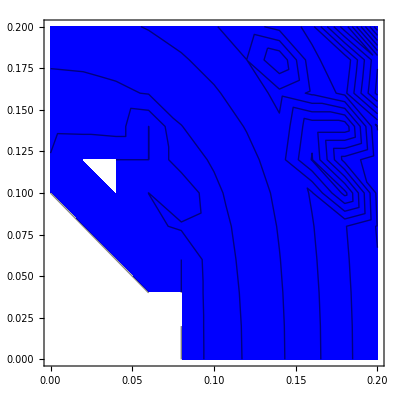

```mathematica
ListContourPlot[Flatten[Chop[datafidDif],1],ColorFunction->(If[#==0,White,If[#>0,Green,Blue]]&),ColorFunctionScaling->False,PlotRange->All]
```

```mathematica
B[0]=Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]};
{B[1],B[2],B[3]}=ArrayReshape[Normalize[RandomReal[{-1,1},12]],{3,4}].Table[σ[i],{i,0,3}];
ρE={{1,0},{0,0}};
{fidDiffopt[0,0.5],fidDiffopt[0.4,0.4]}
```

{-0.00173679,-0.0141281}

```mathematica
fidDiffopt[α_,β_]:=Module[{Ht,U0,UDD,ρS,ρST,ρSTDD,p1,p2,p3},
ρS={1,p1,p2,p3}.{σ[0],σ[1],σ[2],σ[3]};
Ht=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
UDD=16KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
NMinimize[
ρST=Map[Tr,Partition[U0.KroneckerProduct[ρS,ρE].U0†,{2,2}],{2}];
ρSTDD=Map[Tr,Partition[UDD.KroneckerProduct[ρS,ρE].UDD†,{2,2}],{2}];
Re[Tr[ρS.(ρSTDD-ρST)]],{p1,p2,p3}∈Sphere[]][[1]]]
```

```mathematica
AbsoluteTiming[
dataMinExact=
ParallelTable[{α,β,fidDiffopt[α,β]},{α,0,0.5,0.025},{β,0,0.5,0.025}];]
```

{162.687,Null}

```mathematica
Chop[dataMinExact]//MatrixForm
```

((0
0
0) | (0
0.025
0.0000102746) | (0
0.05
0.0000402562) | (0
0.075
0.0000866472) | (0
0.1
0.00014365) | (0
0.125
0.000203252) | (0
0.15
0.00025552) | (0
0.175
0.000288905) | (0
0.2
0.000290553) | (0
0.225
0.000246602) | (0
0.25
0.000142485) | (0
0.275
-0.0000367865) | (0
0.3
-0.000306349) | (0
0.325
-0.000681226) | (0
0.35
-0.00117609) | (0
0.375
-0.00180501) | (0
0.4
-0.00258129) | (0
0.425
-0.00351723) | (0
0.45
-0.00462394) | (0
0.475
-0.00591124) | (0
0.5
-0.00738743)
(0.025
0
0) | (0.025
0.025
0.000010005) | (0.025
0.05
0.000038995) | (0.025
0.075
0.0000834921) | (0.025
0.1
0.000137633) | (0.025
0.125
0.000193434) | (0.025
0.15
0.000241077) | (0.025
0.175
0.000269191) | (0.025
0.2
0.000265154) | (0.025
0.225
0.000215371) | (0.025
0.25
0.000105569) | (0.025
0.275
-0.0000789382) | (0.025
0.3
-0.00035298) | (0.025
0.325
-0.000731284) | (0.025
0.35
-0.00122824) | (0.025
0.375
-0.00185767) | (0.025
0.4
-0.00263266) | (0.025
0.425
-0.00356531) | (0.025
0.45
-0.00466662) | (0.025
0.475
-0.0059463) | (0.025
0.5
-0.00741264)
(0.05
0
0) | (0.05
0.025
9.46538×10^-6) | (0.05
0.05
0.000036579) | (0.05
0.075
0.0000775723) | (0.05
0.1
0.000126406) | (0.05
0.125
0.000175025) | (0.05
0.15
0.000213621) | (0.05
0.175
0.000230908) | (0.05
0.2
0.000214401) | (0.05
0.225
0.000150691) | (0.05
0.25
0.0000257155) | (0.05
0.275
-0.00017498) | (0.05
0.3
-0.00046599) | (0.05
0.325
-0.000861807) | (0.05
0.35
-0.0013766) | (0.05
0.375
-0.002024) | (0.05
0.4
-0.0028169) | (0.05
0.425
-0.00376728) | (0.05
0.45
-0.00488605) | (0.05
0.475
-0.00618287) | (0.05
0.5
-0.00766604)
(0.075
0
0) | (0.075
0.025
8.64899×10^-6) | (0.075
0.05
0.000032983) | (0.075
0.075
0.000068834) | (0.075
0.1
0.000109881) | (0.075
0.125
0.000147889) | (0.075
0.15
0.000172961) | (0.075
0.175
0.000173798) | (0.075
0.2
0.000137963) | (0.075
0.225
0.0000521411) | (0.075
0.25
-0.0000975997) | (0.075
0.275
-0.00032556) | (0.075
0.3
-0.000646169) | (0.075
0.325
-0.00107375) | (0.075
0.35
-0.00162232) | (0.075
0.375
-0.00230535) | (0.075
0.4
-0.00313563) | (0.075
0.425
-0.00412506) | (0.075
0.45
-0.00528448) | (0.075
0.475
-0.00662356) | (0.075
0.5
-0.00815064)
(0.1
0
0) | (0.1
0.025
7.54946×10^-6) | (0.1
0.05
0.0000281837) | (0.1
0.075
0.0000572285) | (0.1
0.1
0.0000879754) | (0.1
0.125
0.000111907) | (0.1
0.15
0.000118938) | (0.1
0.175
0.0000976575) | (0.1
0.2
0.0000355828) | (0.1
0.225
-0.0000805929) | (0.1
0.25
-0.000264755) | (0.1
0.275
-0.000531129) | (0.1
0.3
-0.00089405) | (0.1
0.325
-0.00136775) | (0.1
0.35
-0.00196613) | (0.1
0.375
-0.0027026) | (0.1
0.4
-0.00358987) | (0.1
0.425
-0.0046398) | (0.1
0.45
-0.00586323) | (0.1
0.475
-0.00726987) | (0.1
0.5
-0.00886815)
(0.125
0
0) | (0.125
0.025
6.16083×10^-6) | (0.125
0.05
0.0000221595) | (0.125
0.075
0.000042713) | (0.125
0.1
0.0000606223) | (0.125
0.125
0.000066987) | (0.125
0.15
0.0000514318) | (0.125
0.175
2.34021×10^-6) | (0.125
0.2
-0.0000929084) | (0.125
0.225
-0.000247702) | (0.125
0.25
-0.000475961) | (0.125
0.275
-0.000791916) | (0.125
0.3
-0.00120988) | (0.125
0.325
-0.00174405) | (0.125
0.35
-0.00240831) | (0.125
0.375
-0.00321602) | (0.125
0.4
-0.0041799) | (0.125
0.425
-0.0053118) | (0.125
0.45
-0.00662261) | (0.125
0.475
-0.0081221) | (0.125
0.5
-0.00981883)
(0.15
0
0) | (0.15
0.025
4.47768×10^-6) | (0.15
0.05
0.000014892) | (0.15
0.075
0.0000252517) | (0.15
0.1
0.0000277685) | (0.15
0.125
0.0000130602) | (0.15
0.15
-0.0000296342) | (0.15
0.175
-0.000112232) | (0.15
0.2
-0.000247581) | (0.15
0.225
-0.000449238) | (0.15
0.25
-0.000731242) | (0.15
0.275
-0.0011079) | (0.15
0.3
-0.00159358) | (0.15
0.325
-0.00220252) | (0.15
0.35
-0.00294862) | (0.15
0.375
-0.00384528) | (0.15
0.4
-0.00490525) | (0.15
0.425
-0.00614043) | (0.15
0.45
-0.0075618) | (0.15
0.475
-0.00917923) | (0.15
0.5
-0.0110014)
(0.175
0
0) | (0.175
0.025
2.49527×10^-6) | (0.175
0.05
6.36553×10^-6) | (0.175
0.075
4.81778×10^-6) | (0.175
0.1
-0.0000106209) | (0.175
0.125
-0.0000499089) | (0.175
0.15
-0.000124285) | (0.175
0.175
-0.00024606) | (0.175
0.2
-0.000428396) | (0.175
0.225
-0.0006851) | (0.175
0.25
-0.00103041) | (0.175
0.275
-0.00147879) | (0.175
0.3
-0.00204473) | (0.175
0.325
-0.00274256) | (0.175
0.35
-0.00358627) | (0.175
0.375
-0.00458935) | (0.175
0.4
-0.00576462) | (0.175
0.425
-0.00712407) | (0.175
0.45
-0.00867881) | (0.175
0.475
-0.0104388) | (0.175
0.5
-0.012413)
(0.2
0
0) | (0.2
0.025
2.09721×10^-7) | (0.2
0.05
-3.43119×10^-6) | (0.2
0.075
-0.0000186059) | (0.2
0.1
-0.0000545609) | (0.2
0.125
-0.000121921) | (0.2
0.15
-0.000232491) | (0.2
0.175
-0.000399059) | (0.2
0.2
-0.000635188) | (0.2
0.225
-0.000955017) | (0.2
0.25
-0.00137306) | (0.2
0.275
-0.001904) | (0.2
0.3
-0.00256251) | (0.2
0.325
-0.0033631) | (0.2
0.35
-0.00431988) | (0.2
0.375
-0.00544647) | (0.2
0.4
-0.00675581) | (0.2
0.425
-0.00826004) | (0.2
0.45
-0.00997037) | (0.2
0.475
-0.011897) | (0.2
0.5
-0.0140489)
(0.225
0
0) | (0.225
0.025
-2.38186×10^-6) | (0.225
0.05
-0.0000145051) | (0.225
0.075
-0.0000450246) | (0.225
0.1
-0.000104044) | (0.225
0.125
-0.000202936) | (0.225
0.15
-0.000354156) | (0.225
0.175
-0.000571052) | (0.225
0.2
-0.000867665) | (0.225
0.225
-0.00125854) | (0.225
0.25
-0.00175853) | (0.225
0.275
-0.00238262) | (0.225
0.3
-0.00314572) | (0.225
0.325
-0.00406256) | (0.225
0.35
-0.00514744) | (0.225
0.375
-0.00641414) | (0.225
0.4
-0.00787578) | (0.225
0.425
-0.00954463) | (0.225
0.45
-0.011432) | (0.225
0.475
-0.0135484) | (0.225
0.5
-0.0159028)
(0.25
0
0) | (0.25
0.025
-5.2812×10^-6) | (0.25
0.05
-0.000026858) | (0.25
0.075
-0.0000744309) | (0.25
0.1
-0.000159036) | (0.25
0.125
-0.000292872) | (0.25
0.15
-0.000489121) | (0.25
0.175
-0.000761762) | (0.25
0.2
-0.00112539) | (0.25
0.225
-0.00159502) | (0.25
0.25
-0.00218592) | (0.25
0.275
-0.00291342) | (0.25
0.3
-0.00379275) | (0.25
0.325
-0.00483888) | (0.25
0.35
-0.00606635) | (0.25
0.375
-0.00748914) | (0.25
0.4
-0.00912053) | (0.25
0.425
-0.010973) | (0.25
0.45
-0.0130581) | (0.25
0.475
-0.0153863) | (0.25
0.5
-0.0179669)
(0.275
0
0) | (0.275
0.025
-8.48871×10^-6) | (0.275
0.05
-0.0000404859) | (0.275
0.075
-0.000106803) | (0.275
0.1
-0.000219477) | (0.275
0.125
-0.000391601) | (0.275
0.15
-0.000637151) | (0.275
0.175
-0.000970808) | (0.275
0.2
-0.00140778) | (0.275
0.225
-0.00196362) | (0.275
0.25
-0.00265407) | (0.275
0.275
-0.00349486) | (0.275
0.3
-0.00450157) | (0.275
0.325
-0.00568946) | (0.275
0.35
-0.00707337) | (0.275
0.375
-0.00866746) | (0.275
0.4
-0.0104853) | (0.275
0.425
-0.0125394) | (0.275
0.45
-0.0148416) | (0.275
0.475
-0.0174025) | (0.275
0.5
-0.0202314)
(0.3
0
0) | (0.3
0.025
-0.0000120033) | (0.3
0.05
-0.0000553783) | (0.3
0.075
-0.000142104) | (0.3
0.1
-0.000285277) | (0.3
0.125
-0.000498945) | (0.3
0.15
-0.000797938) | (0.3
0.175
-0.0011977) | (0.3
0.2
-0.00171411) | (0.3
0.225
-0.00236331) | (0.3
0.25
-0.00316157) | (0.3
0.275
-0.00412505) | (0.3
0.3
-0.00526974) | (0.3
0.325
-0.00661124) | (0.3
0.35
-0.00816467) | (0.3
0.375
-0.00994443) | (0.3
0.4
-0.0119643) | (0.3
0.425
-0.014237) | (0.3
0.45
-0.0167746) | (0.3
0.475
-0.0195876) | (0.3
0.5
-0.0226857)
(0.325
0
0) | (0.325
0.025
-0.0000158225) | (0.325
0.05
-0.0000715182) | (0.325
0.075
-0.000180281) | (0.325
0.1
-0.000356316) | (0.325
0.125
-0.000614677) | (0.325
0.15
-0.000971099) | (0.325
0.175
-0.00144184) | (0.325
0.2
-0.00204349) | (0.325
0.225
-0.00279285) | (0.325
0.25
-0.00370672) | (0.325
0.275
-0.00480179) | (0.325
0.3
-0.00609444) | (0.325
0.325
-0.00760065) | (0.325
0.35
-0.00933583) | (0.325
0.375
-0.0113147) | (0.325
0.4
-0.0135512) | (0.325
0.425
-0.0160583) | (0.325
0.45
-0.018848) | (0.325
0.475
-0.0219311) | (0.325
0.5
-0.0253174)
(0.35
0
0) | (0.35
0.025
-0.0000199418) | (0.35
0.05
-0.0000888815) | (0.35
0.075
-0.000221265) | (0.35
0.1
-0.000432444) | (0.35
0.125
-0.000738519) | (0.35
0.15
-0.00115617) | (0.35
0.175
-0.00170252) | (0.35
0.2
-0.00239491) | (0.35
0.225
-0.00325082) | (0.35
0.25
-0.00428764) | (0.35
0.275
-0.00552258) | (0.35
0.3
-0.00697249) | (0.35
0.325
-0.00865372) | (0.35
0.35
-0.010582) | (0.35
0.375
-0.0127723) | (0.35
0.4
-0.0152388) | (0.35
0.425
-0.0179948) | (0.35
0.45
-0.021052) | (0.35
0.475
-0.0244217) | (0.35
0.5
-0.0281136)
(0.375
0
0) | (0.375
0.025
-0.0000243554) | (0.375
0.05
-0.000107437) | (0.375
0.075
-0.000264968) | (0.375
0.1
-0.000513477) | (0.375
0.125
-0.000870143) | (0.375
0.15
-0.00135263) | (0.375
0.175
-0.00197893) | (0.375
0.2
-0.0027672) | (0.375
0.225
-0.00373561) | (0.375
0.25
-0.00490219) | (0.375
0.275
-0.00628466) | (0.375
0.3
-0.00790037) | (0.375
0.325
-0.00976605) | (0.375
0.35
-0.0118978) | (0.375
0.375
-0.0143108) | (0.375
0.4
-0.0170195) | (0.375
0.425
-0.0200372) | (0.375
0.45
-0.0233761) | (0.375
0.475
-0.0270472) | (0.375
0.5
-0.0310601)
(0.4
0
0) | (0.4
0.025
-0.0000290553) | (0.4
0.05
-0.000127146) | (0.4
0.075
-0.000311288) | (0.4
0.1
-0.000599205) | (0.4
0.125
-0.00100918) | (0.4
0.15
-0.00155986) | (0.4
0.175
-0.00227017) | (0.4
0.2
-0.00315907) | (0.4
0.225
-0.00424545) | (0.4
0.25
-0.005548) | (0.4
0.275
-0.00708501) | (0.4
0.3
-0.00887426) | (0.4
0.325
-0.0109329) | (0.4
0.35
-0.0132774) | (0.4
0.375
-0.0159233) | (0.4
0.4
-0.0188851) | (0.4
0.425
-0.0221762) | (0.4
0.45
-0.025809) | (0.4
0.475
-0.0297945) | (0.4
0.5
-0.0341422)
(0.425
0
0) | (0.425
0.025
-0.0000340323) | (0.425
0.05
-0.000147964) | (0.425
0.075
-0.000360106) | (0.425
0.1
-0.000689388) | (0.425
0.125
-0.00115519) | (0.425
0.15
-0.00177721) | (0.425
0.175
-0.00257525) | (0.425
0.2
-0.00356912) | (0.425
0.225
-0.00477845) | (0.425
0.25
-0.00622258) | (0.425
0.275
-0.00792037) | (0.425
0.3
-0.00989011) | (0.425
0.325
-0.0121494) | (0.425
0.35
-0.0147149) | (0.425
0.375
-0.0176025) | (0.425
0.4
-0.0208269) | (0.425
0.425
-0.0244016) | (0.425
0.45
-0.0283391) | (0.425
0.475
-0.0326503) | (0.425
0.5
-0.0373447)
(0.45
0
0) | (0.45
0.025
-0.0000392749) | (0.45
0.05
-0.000169838) | (0.45
0.075
-0.000411289) | (0.45
0.1
-0.000783757) | (0.45
0.125
-0.00130774) | (0.45
0.15
-0.00200393) | (0.45
0.175
-0.00289308) | (0.45
0.2
-0.00399583) | (0.45
0.225
-0.00533256) | (0.45
0.25
-0.00692325) | (0.45
0.275
-0.00878735) | (0.45
0.3
-0.0109436) | (0.45
0.325
-0.0134101) | (0.45
0.35
-0.0162038) | (0.45
0.375
-0.0193408) | (0.45
0.4
-0.022836) | (0.45
0.425
-0.0267032) | (0.45
0.45
-0.0309545) | (0.45
0.475
-0.035601) | (0.45
0.5
-0.0406522)
(0.475
0
0) | (0.475
0.025
-0.0000447706) | (0.475
0.05
-0.000192709) | (0.475
0.075
-0.000464688) | (0.475
0.1
-0.000882023) | (0.475
0.125
-0.00146631) | (0.475
0.15
-0.00223926) | (0.475
0.175
-0.00322254) | (0.475
0.2
-0.00443762) | (0.475
0.225
-0.00590564) | (0.475
0.25
-0.00764722) | (0.475
0.275
-0.00968241) | (0.475
0.3
-0.0120304) | (0.475
0.325
-0.0147097) | (0.475
0.35
-0.0177376) | (0.475
0.375
-0.0211305) | (0.475
0.4
-0.0249035) | (0.475
0.425
-0.0290701) | (0.475
0.45
-0.0336429) | (0.475
0.475
-0.0386329) | (0.475
0.5
-0.044049)
(0.5
0
0) | (0.5
0.025
-0.000050505) | (0.5
0.05
-0.000216514) | (0.5
0.075
-0.000520144) | (0.5
0.1
-0.000983873) | (0.5
0.125
-0.00163038) | (0.5
0.15
-0.00248237) | (0.5
0.175
-0.00356242) | (0.5
0.2
-0.00489283) | (0.5
0.225
-0.00649546) | (0.5
0.25
-0.00839161) | (0.5
0.275
-0.0106019) | (0.5
0.3
-0.013146) | (0.5
0.325
-0.0160427) | (0.5
0.35
-0.0193098) | (0.5
0.375
-0.0229638) | (0.5
0.4
-0.0270199) | (0.5
0.425
-0.0314919) | (0.5
0.45
-0.0363923) | (0.5
0.475
-0.0417318) | (0.5
0.5
-0.0475194))

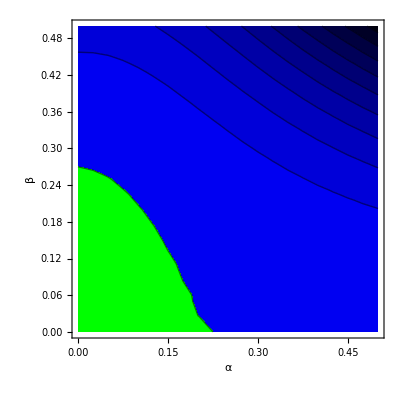

```mathematica
pic2=ListContourPlot[Flatten[Chop[dataMinExact],1],ColorFunction->(If[#<0,Darker[Blue,Abs[20 #]],Lighter[Green,#]]&),ColorFunctionScaling->False,PlotRange->All,
FrameLabel->{α,β}]
```

```mathematica
["/Users/jiaan/Desktop/DD/phase-diag2.pdf",pic2]
```

/Users/jiaan/Desktop/DD/phase-diag2.pdf

```mathematica
pic2=ListContourPlot[Flatten[dataMinExact,1],ColorFunction->(If[#<0,Blue,Green]&),ColorFunctionScaling->False,PlotRange->All,
FrameLabel->{α,β}]
```

```mathematica
MatrixForm@Chop[dataMinExact]
```

((0
0
0) | (0
0.05
-0.000212787) | (0
0.1
-0.00390814) | (0
0.15
-0.0185308) | (0
0.2
-0.0530621) | (0
0.25
-0.115635) | (0
0.3
-0.211504) | (0
0.35
-0.340953) | (0
0.4
-0.496974)
(0.05
0
0) | (0.05
0.05
-0.000337905) | (0.05
0.1
-0.00435298) | (0.05
0.15
-0.019389) | (0.05
0.2
-0.0543073) | (0.05
0.25
-0.117109) | (0.05
0.3
-0.21292) | (0.05
0.35
-0.341937) | (0.05
0.4
-0.497142)
(0.1
0
0) | (0.1
0.05
-0.000733485) | (0.1
0.1
-0.00595874) | (0.1
0.15
-0.0229686) | (0.1
0.2
-0.0604909) | (0.1
0.25
-0.126332) | (0.1
0.3
-0.225371) | (0.1
0.35
-0.357513) | (0.1
0.4
-0.515422)
(0.15
0
0) | (0.15
0.05
-0.00141711) | (0.15
0.1
-0.00881354) | (0.15
0.15
-0.0295116) | (0.15
0.2
-0.0721208) | (0.15
0.25
-0.144211) | (0.15
0.3
-0.250293) | (0.15
0.35
-0.389752) | (0.15
0.4
-0.554577)
(0.2
0
0) | (0.2
0.05
-0.00241004) | (0.2
0.1
-0.0130209) | (0.2
0.15
-0.0392954) | (0.2
0.2
-0.0897602) | (0.2
0.25
-0.1717) | (0.2
0.3
-0.289099) | (0.2
0.35
-0.440524) | (0.2
0.4
-0.616861)
(0.25
0
0) | (0.25
0.05
-0.00372449) | (0.25
0.1
-0.0186368) | (0.25
0.15
-0.0524571) | (0.25
0.2
-0.113652) | (0.25
0.25
-0.202914) | (0.25
0.3
-0.331472) | (0.25
0.35
-0.493378) | (0.25
0.4
-0.67788)
(0.3
0
0) | (0.3
0.05
-0.00534827) | (0.3
0.1
-0.0255953) | (0.3
0.15
-0.0672532) | (0.3
0.2
-0.139672) | (0.3
0.25
-0.248485) | (0.3
0.3
-0.395641) | (0.3
0.35
-0.57679) | (0.3
0.4
-0.779296)
(0.35
0
0) | (0.35
0.05
-0.00723271) | (0.35
0.1
-0.0331499) | (0.35
0.15
-0.0860007) | (0.35
0.2
-0.173579) | (0.35
0.25
-0.301216) | (0.35
0.3
-0.469532) | (0.35
0.35
-0.672368) | (0.35
0.4
-0.895147)
(0.4
0
0) | (0.4
0.05
-0.00929063) | (0.4
0.1
-0.041877) | (0.4
0.15
-0.106338) | (0.4
0.2
-0.210137) | (0.4
0.25
-0.357667) | (0.4
0.3
-0.548043) | (0.4
0.35
-0.773237) | (0.4
0.4
-1.0169))

```mathematica
BB=Table[Tr[B[i].B[j].ρE],{i,1,3},{j,1,3}]//Chop;
M=2Tr[BB]*IdentityMatrix[3]-2Re[BB];
t=-4{Im[BB][[2,3]],Im[BB][[3,1]],Im[BB][[1,2]]};
```

```mathematica
NMinimize[t.{p1,p2,p3}+{p1,p2,p3}.M.{p1,p2,p3},{p1,p2,p3}∈Sphere[]]
```

{0.552936,{p1→-0.650072,p2→0.298947,p3→0.698597}}

```mathematica
BDD[1]=-4ⅈ α β cm[B[0],B[1]]//Chop;
BDD[2]=-2ⅈ α β cm[B[0],B[2]]+2 β^2 am[B[1],B[3]]//Chop;
BDD[3]={{0,0},{0,0}};
BBDD=Collect[β^-2 Table[Tr[BDD[i].BDD[j].ρE],{i,1,3},{j,1,3}],{α,β},Chop];MatrixForm@BBDD
```

(1.13693 α^2 | (-1.89783+0.697006 ⅈ) α^2-(0.317205-0.156321 ⅈ) α β | 0
(-1.89783-0.697006 ⅈ) α^2-(0.317205+0.156321 ⅈ) α β | 3.79425 α^2+2.63095 α β+2.56164 β^2 | 0
0 | 0 | 0)

```mathematica
MDD=Simplify[ComplexExpand[2Tr[BBDD]*IdentityMatrix[3]-2Re[BBDD]],{α,β}∈Reals]//Chop;
tDD=Simplify[ComplexExpand[-4{Im[BBDD][[2,3]],Im[BBDD][[3,1]],Im[BBDD][[1,2]]}],{α,β}∈Reals]//Chop;
```

```mathematica
M-MDD//MatrixForm
```

(2.40286-7.58851 α^2-5.26189 α β-5.12328 β^2 | 0.169397-3.79566 α^2-0.63441 α β | 0.794528
0.169397-3.79566 α^2-0.63441 α β | 1.93-2.27385 α^2 | -0.309622
0.794528 | -0.309622 | 1.32599-9.86236 α^2-5.26189 α β-5.12328 β^2)

```mathematica
AbsoluteTiming[dataMinApp=ParallelTable[{α,β,
NMinimize[(t-tDD).{p1,p2,p3}+{p1,p2,p3}.(M-MDD).{p1,p2,p3},{p1,p2,p3}∈Sphere[]][[1]]},{α,0,0.5,0.025},{β,0,0.5,0.025}];]
```

{107.263,Null}

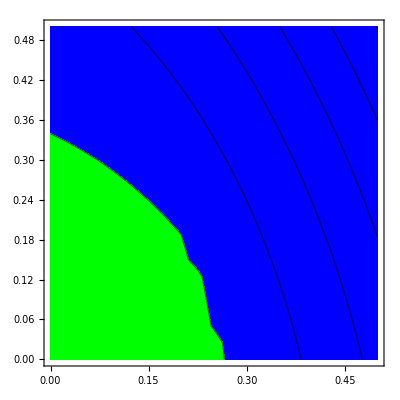

```mathematica
ListContourPlot[Flatten[dataMinApp,1],ColorFunction->(If[#<0,Blue,Green]&),ColorFunctionScaling->False,PlotRange->All]
```

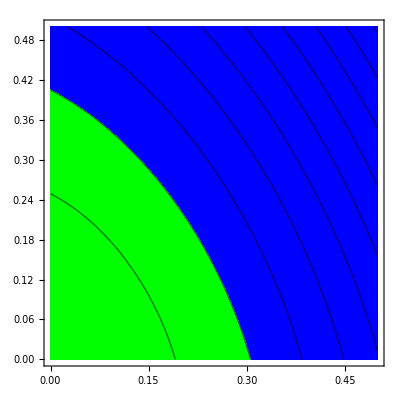

```mathematica
ContourPlot[
Min[Eigenvalues[M-MDD/.{α->x,β->y}]],{x,0,0.5},{y,0,0.5},ColorFunction->(If[#<0,Blue,Green]&),ColorFunctionScaling->False]
```

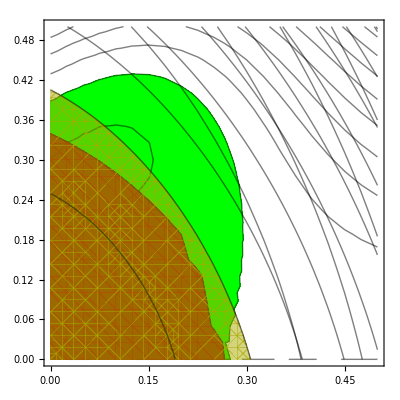

```mathematica
Show[ListContourPlot[Flatten[dataMinExact,1],ColorFunction->(If[#<0,Transparent,Green]&),ColorFunctionScaling->False,PlotRange->All],ListContourPlot[Flatten[dataMinApp,1],ColorFunction->(If[#<0,Transparent,Opacity[0.85,Darker[Red]]]&),ColorFunctionScaling->False,PlotRange->All],
ContourPlot[Min[Eigenvalues[M-MDD/.{α->x,β->y}]],{x,0,0.5},{y,0,0.5},ColorFunction->(If[#<0,Transparent,Opacity[0.5,Darker[Yellow]]]&),ColorFunctionScaling->False]]
```

```mathematica
{A[0],A[1],A[2],A[3]}={1/(√2){{0,1},{1,0}},{{1,0},{0,0}},1/(√2){{1,0},{0,-1}},{{1,0},{0,0}}};
ρE={{1,0},{0,0}};
```

```mathematica
Norm[#,"Frobenius"]&/@{A[0],A[1],A[2],A[3]}
```

{1,1,1,1}

```mathematica
MatrixForm/@{A[0],A[1],A[2],A[3]}
```

{(0 | 1/(√2)
1/(√2) | 0),(1 | 0
0 | 0),(1/(√2) | 0
0 | -1/(√2)),(1 | 0
0 | 0)}

```mathematica
ρE={{1,0},{0,0}};MatrixForm[ρE]
```

```mathematica
Tr[ρE.A[3]]
```

1

```mathematica
AA=Table[Tr[A[i].A[j].ρE],{i,1,3},{j,1,3}]
```

{{1,1/(√2),1},{1/(√2),1/2,1/(√2)},{1,1/(√2),1}}

```mathematica
MA0=2Tr[AA]*IdentityMatrix[3]-2Re[AA]
```

{{3,-√2,-2},{-√2,4,-√2},{-2,-√2,3}}

```mathematica
Eigenvalues[MA0]
```

{5,5,0}

```mathematica
tA0=ComplexExpand[-4{Im[AA][[2,3]],Im[AA][[3,1]],Im[AA][[1,2]]}]
```

{0,0,0}

```mathematica
MatrixForm/@Simplify[NestList[cm[σ[1],#]&,A[1],5]]
```

{(1 | 0
0 | 0),(0 | -1
1 | 0),(2 | 0
0 | -2),(0 | -4
4 | 0),(8 | 0
0 | -8),(0 | -16
16 | 0)}

```mathematica
AD[1]=Simplify[α^n β(-ⅈ)^n 2^(n(n+1))Nest[cm[A[0],#]&,A[1],n]/.n->2];
AD[2]=Expand[α^(n-1)β(-ⅈ)^n 2^(n^2)Nest[cm[A[0],#]&,(α cm[A[0],A[2]]+ⅈ β am[A[1],A[3]]),n-1]/.n->2];
AD[3]=0 IdentityMatrix[2];
AAD=Table[Tr[AD[i].AD[j].ρE],{i,1,3},{j,1,3}];
MAAD=ComplexExpand[2Tr[AAD]IdentityMatrix[3]-2Re[AAD]]
```

{{1024 α^4 β^2+1024 α^2 β^4,-2048 √2 α^4 β^2,0},{-2048 √2 α^4 β^2,8192 α^4 β^2,0},{0,0,9216 α^4 β^2+1024 α^2 β^4}}

```mathematica
Collect[1/2{p1,p2,p3}.(MAAD).{p1,p2,p3}/.{p1->√(2/5),p2->1/(√5),p3->√(2/5)},{α,β},Simplify]
```

2048 α^4 β^2+(2048 α^2 β^4)/5

```mathematica
Simplify[(2048 α^4 β^2+(2048 α^2 β^4)/5)/(1/20 α^2 β^2)]
```

8192 (5 α^2+β^2)

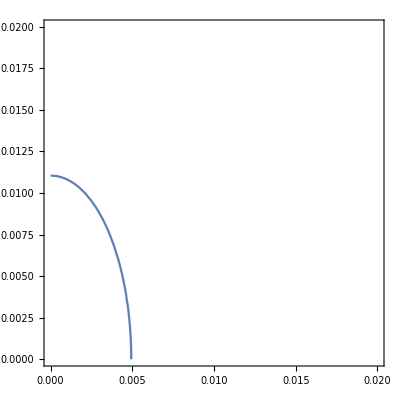

```mathematica
ContourPlot[8192 (5 α^2+β^2)==1,{α,0,0.02},{β,0,0.02}]
```

```mathematica
√(1./(5*8192))
```

0.00494106

```mathematica
FactorInteger[8192]
```

{{2,13}}

```mathematica
Simplify[1/2{1,p1,p2,p3}.{σ[0],σ[1],σ[2],σ[3]}/.{p1->√(2/5),p2->1/(√5),p3->√(2/5)}]
```

{{1/2+1/(√10),(-ⅈ+√2)/(2 √5)},{(ⅈ+√2)/(2 √5),1/2-1/(√10)}}

```mathematica
NMinimize[{Simplify[{p1,p2,p3}.(MA0-MAAD).{p1,p2,p3}/.{α->0.1,β->0.2}],a1^2+a2^2≤ 1&&p1^2+p2^2+p3^2==1},{a1,a2,a3,p1,p2,p3}]
```

{-0.786005,{a1→-0.765207,a2→0.643785,a3→1.1666,p1→-0.573848,p2→-0.414497,p3→-0.706322}}

```mathematica
Minimize[{3 p1^2-2 √2 p1 p2+4 p2^2-4 p1 p3-2 √2 p2 p3+3 p3^2,p1^2+p2^2+p3^2==1},{p1,p2,p3}]
```

{0,{p1→-√(2/5),p2→-1/(√5),p3→-√(2/5)}}

```mathematica
a1^2+a2^2+a3^2/.%1869[[2]]
```

1.

```mathematica
(MA0-MAAD)/.{α->0.1,β->0.1}/.%1869[[2]]
```

{{2.79989,-1.13121,-2},{-1.13121,3.19956,-√2},{-2,-√2,1.99944}}

```mathematica
{0,a1,a2,a3}.{σ[0],σ[1],σ[2],σ[3]}/√2/.%1885[[2]]//MatrixForm
```

(-4.92707×10^-9 | 0.276864+0.650651 ⅈ
0.276864-0.650651 ⅈ | 4.92707×10^-9)

```mathematica
Eigensystem[MA0]
```

{{5,5,0},{{-1,0,1},{-1/(√2),1,0},{1,1/(√2),1}}}

```mathematica
Module[{α=0.1,UDD,ρS,ρST,ρSTDD},
ρS=Simplify[1/2{1,p1,p2,p3}.{σ[0],σ[1],σ[2],σ[3]}/.{p1->√(2/5),p2->1/(√5),p3->√(2/5)}];
dataFreeMin=Table[{t,
Ht=0.1 t*KroneckerProduct[σ[0],A[0]]+0.1 t*Sum[KroneckerProduct[σ[i],A[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
ρST=Map[Tr,Partition[U0.KroneckerProduct[ρS,ρE].U0†,{2,2}],{2}];
1-Re[Tr[ρS.ρST]]},{t,0,0.5,0.01}]]
```

{{0.,-2.22045×10^-16},{0.01,4.9738×10^-14},{0.02,8.00138×10^-13},{0.03,4.04965×10^-12},{0.04,1.27998×10^-11},{0.05,3.12497×10^-11},{0.06,6.47989×10^-11},{0.07,1.20048×10^-10},{0.08,2.04796×10^-10},{0.09,3.28041×10^-10},{0.1,4.99983×10^-10},{0.11,7.3202×10^-10},{0.12,1.03675×10^-9},{0.13,1.42797×10^-9},{0.14,1.92067×10^-9},{0.15,2.53106×10^-9},{0.16,3.27652×10^-9},{0.17,4.17565×10^-9},{0.18,5.24823×10^-9},{0.19,6.51527×10^-9},{0.2,7.99893×10^-9},{0.21,9.72262×10^-9},{0.22,1.17109×10^-8},{0.23,1.39896×10^-8},{0.24,1.65856×10^-8},{0.25,1.95272×10^-8},{0.26,2.28437×10^-8},{0.27,2.65656×10^-8},{0.28,3.07248×10^-8},{0.29,3.53541×10^-8},{0.3,4.04879×10^-8},{0.31,4.61613×10^-8},{0.32,5.24109×10^-8},{0.33,5.92745×10^-8},{0.34,6.67911×10^-8},{0.35,7.50006×10^-8},{0.36,8.39445×10^-8},{0.37,9.36653×10^-8},{0.38,1.04207×10^-7},{0.39,1.15613×10^-7},{0.4,1.27932×10^-7},{0.41,1.41209×10^-7},{0.42,1.55493×10^-7},{0.43,1.70835×10^-7},{0.44,1.87284×10^-7},{0.45,2.04893×10^-7},{0.46,2.23715×10^-7},{0.47,2.43804×10^-7},{0.48,2.65217×10^-7},{0.49,2.88009×10^-7},{0.5,3.1224×10^-7}}

```mathematica
Fit[Log[Rest[dataFreeMin]],{1,x},x]
```

-12.2062+4.00017 x

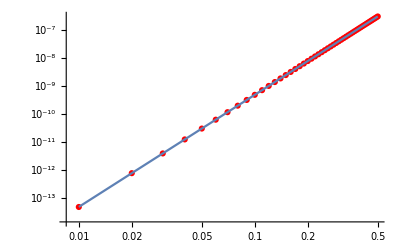

```mathematica
Show[ListLogLogPlot[dataFreeMin,PlotStyle->Red],LogLogPlot[0.1^4/20 x^4,{x,0.01,0.5}]]
```

```mathematica
Simplify[MA0.{√(2/5),1/(√5),√(2/5)}]
```

{0,0,0}

```mathematica
Ht=α KroneckerProduct[σ[0],A[0]]+β Sum[KroneckerProduct[σ[i],A[i]],{i,1,3}]
```

{{β,α/(√2),(1-ⅈ/(√2)) β,0},{α/(√2),0,0,(ⅈ β)/(√2)},{(1+ⅈ/(√2)) β,0,-β,α/(√2)},{0,-(ⅈ β)/(√2),α/(√2),0}}

```mathematica
Simplify[cm[Ht,cm[Ht,KroneckerProduct[ρSmin,ρE]]]]//MatrixForm
```

(1/10 (5+√10) α^2 | -1/20 ⅈ (-5 ⅈ √2-6 ⅈ √5+√10) α β | ((-ⅈ+√2) α^2)/(2 √5) | 1/20 ⅈ (10+5 ⅈ √2+√10) α β
1/20 ⅈ (5 ⅈ √2+6 ⅈ √5+√10) α β | -1/10 (5+√10) α^2 | -1/20 ⅈ (-10-5 ⅈ √2+√10) α β | -((-ⅈ+√2) α^2)/(2 √5)
((ⅈ+√2) α^2)/(2 √5) | 1/20 ⅈ (-10+5 ⅈ √2+√10) α β | -1/10 (-5+√10) α^2 | 1/20 (5 √2-6 √5+ⅈ √10) α β
-1/20 ⅈ (10-5 ⅈ √2+√10) α β | -((ⅈ+√2) α^2)/(2 √5) | 1/20 (5 √2-6 √5-ⅈ √10) α β | 1/10 (-5+√10) α^2)

```mathematica
Simplify[Map[Tr,Partition[Simplify[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]],{2,2}],{2}]]//MatrixForm
```

(-(ⅈ α^2 β)/(√5) | (ⅈ α^2 β)/(√5)
(ⅈ α^2 β)/(√5) | (ⅈ α^2 β)/(√5))

```mathematica
ρSmin
```

{{1/2+1/(√10),(-ⅈ+√2)/(2 √5)},{(ⅈ+√2)/(2 √5),1/2-1/(√10)}}

```mathematica
Simplify[Tr[ρSmin.Map[Tr,Partition[Simplify[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]],{2,2}],{2}]]]
```

0

```mathematica
Simplify[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]]//MatrixForm
```

((ⅈ α^2 β)/(2 √5) | -1/10 α ((5 √2+2 √5) α^2+(5 ⅈ+10 √2+3 √5) β^2) | -(ⅈ α^2 β)/(2 √5) | 1/10 ⅈ (√5 (2 ⅈ+√2) α^3+(5+3 ⅈ √5+4 √10) α β^2)
1/10 α ((5 √2+2 √5) α^2+(-5 ⅈ+10 √2+3 √5) β^2) | -(3 ⅈ α^2 β)/(2 √5) | 1/10 (√5 (2-ⅈ √2) α^3+(5 ⅈ+3 √5-4 ⅈ √10) α β^2) | (3 ⅈ α^2 β)/(2 √5)
-(ⅈ α^2 β)/(2 √5) | -1/10 ⅈ (√5 (-2 ⅈ+√2) α^3+(-5-3 ⅈ √5+4 √10) α β^2) | -(ⅈ α^2 β)/(2 √5) | 1/10 ((-5 √2+2 √5) α^3+(5 ⅈ-10 √2+3 √5) α β^2)
1/10 (√5 (2+ⅈ √2) α^3+(5 ⅈ+3 √5+4 ⅈ √10) α β^2) | (3 ⅈ α^2 β)/(2 √5) | 1/10 α ((5 √2-2 √5) α^2+(5 ⅈ+10 √2-3 √5) β^2) | (3 ⅈ α^2 β)/(2 √5))

```mathematica
Map[Tr,Partition[Simplify[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]],{2,2}],{2}]//MatrixForm
```

(-(ⅈ α^2 β)/(√5) | (ⅈ α^2 β)/(√5)
(ⅈ α^2 β)/(√5) | (ⅈ α^2 β)/(√5))

```mathematica
Map[Tr,Partition[Simplify[Nest[cm[Ht,#]&,KroneckerProduct[{{0,0},{0,1}},ρE],3]],{2,2}],{2}]//MatrixForm
```

```mathematica
Simplify[1/24 Tr[ρSmin.Map[Tr,Partition[Simplify[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],4]],{2,2}],{2}]]]//Chop
```

-1/20 α^2 β^2

```mathematica
{B[0],B[1],B[2],B[3]}=Table[
Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]}/√2,{i,1,4}];
```

```mathematica
Ht=0.1 *KroneckerProduct[σ[0],A[0]]+0.1 *Sum[KroneckerProduct[σ[i],A[i]],{i,1,3}];
```

```mathematica
Simplify[Reduce[ (5 α^2+(β(1+θ))^2)<ϵ^2,θ,Reals],α>0&&β>0&&ϵ>0]
```

β+√(-5 α^2+ϵ^2)+β θ>0&&√(-5 α^2+ϵ^2)>β+β θ&&ϵ>√5 α

{}

```mathematica
Simplify[Series[(-128 β^2+√2 √(β^2-40960 α^2 β^2))/(128 β^2),{α,0,2}],β>0]
```

(-1+1/(64 √2 β))-(160 √2 α^2)/β+O[α]^3

```mathematica
βc=√(1/(8192))
```

1/(64 √2)

```mathematica
αc=√(1/(5*8192))
```

1/(64 √10)

```mathematica
Simplify[(-128 β^2+√2 √(β^2-40960 α^2 β^2))/(128 β^2)/.{β->βt βc,α->αt αc},αt>0&&βt>0]
```

-1+(√(1-αt^2))/βt

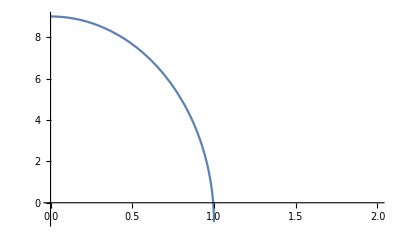

```mathematica
Plot[-1+(√(1-αt^2))/βt/.βt->0.1,{αt,0,2}]
```

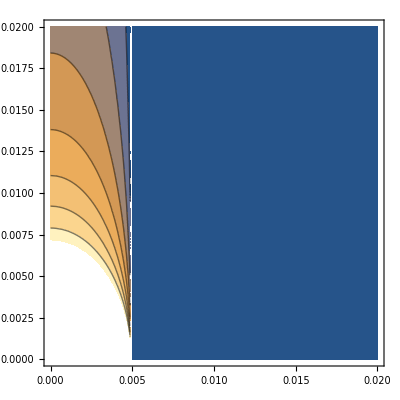

```mathematica
ContourPlot[Piecewise[{{(-128 β^2+√2 √(β^2-40960 α^2 β^2))/(128 β^2),α<=αc}},-1],{α,0,0.02},{β,0,0.02}]
```

```mathematica
{B[0],B[1],B[2],B[3]}=Table[
Normalize[RandomReal[{-1,1},4]].{σ[0],σ[1],σ[2],σ[3]}/√2,{i,1,4}];
```

```mathematica
Ht=α KroneckerProduct[σ[0],A[0]]+β Sum[KroneckerProduct[σ[i],A[i]],{i,1,3}]
```

{{β,α/(√2),(1-ⅈ/(√2)) β,0},{α/(√2),0,0,(ⅈ β)/(√2)},{(1+ⅈ/(√2)) β,0,-β,α/(√2)},{0,-(ⅈ β)/(√2),α/(√2),0}}

```mathematica
TrB[X_]:=Map[Tr,Partition[X,{2,2}],{2}]
```

```mathematica
TrB[KroneckerProduct[ρS,ρE]]
```

{{0.325826+0. ⅈ,-0.315703+0.346403 ⅈ},{-0.315703-0.346403 ⅈ,0.674174+0. ⅈ}}

```mathematica
Simplify[Tr[ρSmin.TrB[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],4]]]]//Chop
```

-6/5 α^2 β^2

```mathematica
TrB[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]]//Simplify
```

{{-(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)},{(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)}}

```mathematica
CM2=Collect[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],2],{α,β},ComplexExpand];MatrixForm@CM2
```

((1/2+1/(√10)) α^2 | (-1/(2 √2)-3/(2 √5)-ⅈ/(2 √10)) α β | (-ⅈ/(2 √5)+1/(√10)) α^2 | (-1/(2 √2)+ⅈ (1/2+1/(2 √10))) α β
(-1/(2 √2)-3/(2 √5)+ⅈ/(2 √10)) α β | (-1/2-1/(√10)) α^2 | (-1/(2 √2)+ⅈ (1/2-1/(2 √10))) α β | (ⅈ/(2 √5)-1/(√10)) α^2
(ⅈ/(2 √5)+1/(√10)) α^2 | (-1/(2 √2)+ⅈ (-1/2+1/(2 √10))) α β | (1/2-1/(√10)) α^2 | (1/(2 √2)-3/(2 √5)+ⅈ/(2 √10)) α β
(-1/(2 √2)+ⅈ (-1/2-1/(2 √10))) α β | (-ⅈ/(2 √5)-1/(√10)) α^2 | (1/(2 √2)-3/(2 √5)-ⅈ/(2 √10)) α β | (-1/2+1/(√10)) α^2)

```mathematica
{At0,At1,At2,At3}=Flatten[Partition[CM2,{2,2}],1];MatrixForm/@{At0,At1,At2,At3}
```

{((1/2+1/(√10)) α^2 | (-1/(2 √2)-3/(2 √5)-ⅈ/(2 √10)) α β
(-1/(2 √2)-3/(2 √5)+ⅈ/(2 √10)) α β | (-1/2-1/(√10)) α^2),((-ⅈ/(2 √5)+1/(√10)) α^2 | (-1/(2 √2)+ⅈ (1/2+1/(2 √10))) α β
(-1/(2 √2)+ⅈ (1/2-1/(2 √10))) α β | (ⅈ/(2 √5)-1/(√10)) α^2),((ⅈ/(2 √5)+1/(√10)) α^2 | (-1/(2 √2)+ⅈ (-1/2+1/(2 √10))) α β
(-1/(2 √2)+ⅈ (-1/2-1/(2 √10))) α β | (-ⅈ/(2 √5)-1/(√10)) α^2),((1/2-1/(√10)) α^2 | (1/(2 √2)-3/(2 √5)+ⅈ/(2 √10)) α β
(1/(2 √2)-3/(2 √5)-ⅈ/(2 √10)) α β | (-1/2+1/(√10)) α^2)}

```mathematica
TrB[CM2]//Simplify
```

{{0,0},{0,0}}

```mathematica
Table[Tr[σ[i].TrB[CM2]],{i,1,3}]//Simplify
```

{0,0,0}

```mathematica
Sum[KroneckerProduct[σ[i],At[i]],{i,0,3}]-Collect[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],2],{α,β},ComplexExpand]//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm/@{At[0],At[1],At[2],At[3]}
```

{(α^2/2 | -(3 α β)/(2 √5)
-(3 α β)/(2 √5) | -α^2/2),(α^2/(√10) | (ⅈ (5 ⅈ+√5) α β)/(10 √2)
-(ⅈ (-5 ⅈ+√5) α β)/(10 √2) | -α^2/(√10)),(α^2/(2 √5) | -(α β)/2
-(α β)/2 | -α^2/(2 √5)),(α^2/(√10) | -(ⅈ (-5 ⅈ+√5) α β)/(10 √2)
(ⅈ (5 ⅈ+√5) α β)/(10 √2) | -α^2/(√10))}

```mathematica
tH
```

tH

```mathematica
Simplify[At[1]/√(2/5)]
```

{{α^2/2,-1/4 (-ⅈ+√5) α β},{-1/4 (ⅈ+√5) α β,-α^2/2}}

```mathematica
Simplify[At[2]/√(1/5)]
```

{{α^2/2,-1/2 √5 α β},{-1/2 √5 α β,-α^2/2}}

```mathematica
Simplify[At[3]/√(2/5)]
```

{{α^2/2,-1/4 (ⅈ+√5) α β},{-1/4 (-ⅈ+√5) α β,-α^2/2}}

```mathematica
Ht//MatrixForm
```

(β | α/(√2) | (1-ⅈ/(√2)) β | 0
α/(√2) | 0 | 0 | (ⅈ β)/(√2)
(1+ⅈ/(√2)) β | 0 | -β | α/(√2)
0 | -(ⅈ β)/(√2) | α/(√2) | 0)

```mathematica
TrB[Ht]//Simplify
```

{{β,β},{β,-β}}

```mathematica
ρSmin
```

{{1/2+1/(√10),(-ⅈ+√2)/(2 √5)},{(ⅈ+√2)/(2 √5),1/2-1/(√10)}}

```mathematica
{√(2/5),1/(√5),√(2/5)}
```

```mathematica
Table[cm[TrB[Ht.KroneckerProduct[σ[0],At[i]]],σ[i]],{i,0,3}]//Simplify
```

{{{0,0},{0,0}},{{-(2 ⅈ α^2 β)/(√5),√(2/5) α^2 β},{-√(2/5) α^2 β,(2 ⅈ α^2 β)/(√5)}},{{(ⅈ α^2 β)/(√5),-(ⅈ α^2 β)/(√5)},{-(ⅈ α^2 β)/(√5),-(ⅈ α^2 β)/(√5)}},{{0,-((-2 ⅈ+√2) α^2 β)/(√5)},{((2 ⅈ+√2) α^2 β)/(√5),0}}}

```mathematica
TrB[cm[Ht,Sum[KroneckerProduct[σ[i],At[i]],{i,0,3}]]]//Simplify
```

{{-(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)},{(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)}}

```mathematica
Total[%2382,1]
```

{{-(ⅈ α^2 β)/(√5),√(2/5) α^2 β-(ⅈ α^2 β)/(√5)-((-2 ⅈ+√2) α^2 β)/(√5)},{-√(2/5) α^2 β-(ⅈ α^2 β)/(√5)+((2 ⅈ+√2) α^2 β)/(√5),(ⅈ α^2 β)/(√5)}}

```mathematica
Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],2]//Simplify//MatrixForm
```

(1/10 (5+√10) α^2 | -1/20 ⅈ (-5 ⅈ √2-6 ⅈ √5+√10) α β | ((-ⅈ+√2) α^2)/(2 √5) | 1/20 ⅈ (10+5 ⅈ √2+√10) α β
1/20 ⅈ (5 ⅈ √2+6 ⅈ √5+√10) α β | -1/10 (5+√10) α^2 | -1/20 ⅈ (-10-5 ⅈ √2+√10) α β | -((-ⅈ+√2) α^2)/(2 √5)
((ⅈ+√2) α^2)/(2 √5) | 1/20 ⅈ (-10+5 ⅈ √2+√10) α β | -1/10 (-5+√10) α^2 | 1/20 (5 √2-6 √5+ⅈ √10) α β
-1/20 ⅈ (10-5 ⅈ √2+√10) α β | -((ⅈ+√2) α^2)/(2 √5) | 1/20 (5 √2-6 √5-ⅈ √10) α β | 1/10 (-5+√10) α^2)

```mathematica
|
```

```mathematica
ρS=1/2σ[0]+1/2Normalize[RandomReal[{-1,1},3]].{σ[1],σ[2],σ[3]}
```

{{0.325826+0. ⅈ,-0.315703+0.346403 ⅈ},{-0.315703-0.346403 ⅈ,0.674174+0. ⅈ}}

```mathematica
cm[Ht,KroneckerProduct[ρS,ρE]]//MatrixForm
```

(0.+0.666812 ⅈ | -0.251552+0.0713061 ⅈ | 0.391084-0.796998 ⅈ | 0.165974+0.334134 ⅈ
0.251552+0.0713061 ⅈ | 0.+0. ⅈ | -0.319546+0.198348 ⅈ | 0.+0. ⅈ
-0.391084-0.796998 ⅈ | 0.319546+0.198348 ⅈ | 0.-0.666812 ⅈ | 0.194418-0.500209 ⅈ
-0.165974+0.334134 ⅈ | 0.+0. ⅈ | -0.194418-0.500209 ⅈ | 0.+0. ⅈ)

```mathematica
Tr[ρS.TrB[cm[Ht,cm[Ht,KroneckerProduct[ρS,ρE]]]]]//Chop
```

3.36517

```mathematica
Tr[ρS.TrB[Nest[cm[Ht,#]&,KroneckerProduct[ρS,ρE],1]]]
```

0.-5.55112×10^-17 ⅈ

```mathematica
Simplify[Tr[ρSmin.TrB[cm[RandomInteger[{0,2},{4,4}],CM2]]]]
```

1/10 ⅈ (2-3 √10) α β

```mathematica
Ht
```

{{β,α/(√2),(1-ⅈ/(√2)) β,0},{α/(√2),0,0,(ⅈ β)/(√2)},{(1+ⅈ/(√2)) β,0,-β,α/(√2)},{0,-(ⅈ β)/(√2),α/(√2),0}}

```mathematica
Ht2= KroneckerProduct[σ[0],B[0]]+ Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}]
```

{{-0.046552+0. ⅈ,0.613669-0.586708 ⅈ,-0.307535-0.718635 ⅈ,-0.289997-1.02893 ⅈ},{0.613669+0.586708 ⅈ,-0.344213+0. ⅈ,0.114849+0.253638 ⅈ,-0.259984-0.317923 ⅈ},{-0.307535+0.718635 ⅈ,0.114849-0.253638 ⅈ,1.53156+0. ⅈ,0.104504+0.111124 ⅈ},{-0.289997+1.02893 ⅈ,-0.259984+0.317923 ⅈ,0.104504-0.111124 ⅈ,-0.213327+0. ⅈ}}

```mathematica
RandomInteger[{0,2},{4,4}]
```

{{0,2,1,2},{2,1,2,2},{2,1,2,1},{1,0,1,2}}

```mathematica
Simplify[Tr[ρSmin.TrB[cm[RandomInteger[{0,2},{4,4}],KroneckerProduct[ρSmin,ρE]]]]]
```

0

```mathematica
Simplify[Tr[ρSmin.TrB[cm[RandomInteger[{0,2},{4,4}],CM2]]]]
```

-(ⅈ α β)/(√10)

```mathematica
cm[Ht,CM2]//Simplify
```

{{(ⅈ α^2 β)/(2 √5),-1/10 α ((5 √2+2 √5) α^2+(5 ⅈ+10 √2+3 √5) β^2),-(ⅈ α^2 β)/(2 √5),1/10 ⅈ (√5 (2 ⅈ+√2) α^3+(5+3 ⅈ √5+4 √10) α β^2)},{1/10 α ((5 √2+2 √5) α^2+(-5 ⅈ+10 √2+3 √5) β^2),-(3 ⅈ α^2 β)/(2 √5),1/10 (√5 (2-ⅈ √2) α^3+(5 ⅈ+3 √5-4 ⅈ √10) α β^2),(3 ⅈ α^2 β)/(2 √5)},{-(ⅈ α^2 β)/(2 √5),-1/10 ⅈ (√5 (-2 ⅈ+√2) α^3+(-5-3 ⅈ √5+4 √10) α β^2),-(ⅈ α^2 β)/(2 √5),1/10 ((-5 √2+2 √5) α^3+(5 ⅈ-10 √2+3 √5) α β^2)},{1/10 (√5 (2+ⅈ √2) α^3+(5 ⅈ+3 √5+4 ⅈ √10) α β^2),(3 ⅈ α^2 β)/(2 √5),1/10 α ((5 √2-2 √5) α^2+(5 ⅈ+10 √2-3 √5) β^2),(3 ⅈ α^2 β)/(2 √5)}}

```mathematica
CM3TrB=TrB[Nest[cm[Ht,#]&,KroneckerProduct[ρSmin,ρE],3]]//Simplify
```

{{-(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)},{(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)}}

```mathematica
am[CM3TrB,ρSmin]//Simplify
```

{{-(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)},{(ⅈ α^2 β)/(√5),(ⅈ α^2 β)/(√5)}}

```mathematica
cm[CM3TrB,ρSmin]//Simplify
```

{{-(α^2 β)/5,-1/5 ⅈ (-ⅈ+2 √2) α^2 β},{1/5 ⅈ (ⅈ+2 √2) α^2 β,(α^2 β)/5}}

```mathematica
Det[ρSmin]
```

0

```mathematica
MatrixRank[{{1/2+1/(√10),(-ⅈ+√2)/(2 √5)},{(ⅈ+√2)/(2 √5),1/2-1/(√10)}}]
```

1

```mathematica
V=Transpose[Eigenvectors[ρSmin]]
```

{{-(-ⅈ √5+√10)/(-5+√10),-(-ⅈ √5+√10)/(5+√10)},{1,1}}

```mathematica
Eigensystem[ρSmin]
```

{{1,0},{{-(-ⅈ √5+√10)/(-5+√10),1},{-(-ⅈ √5+√10)/(5+√10),1}}}

```mathematica
ρSmin//Simplify
```

{{1/2+1/(√10),(-ⅈ+√2)/(2 √5)},{(ⅈ+√2)/(2 √5),1/2-1/(√10)}}

```mathematica
Inverse[V].ρSmin.V//Simplify
```

{{1,0},{0,0}}

```mathematica
Inverse[V].CM3TrB.V//Simplify
```

{{0,-(ⅈ (-5+√10) (5-ⅈ √5+2 √10) α^2 β)/(5 (-ⅈ+√2) (5+√10))},{-(ⅈ (5+√10) (-5-ⅈ √5+2 √10) α^2 β)/(5 (-ⅈ+√2) (-5+√10)),0}}

```mathematica
cm[{{a,b},{c,d}},ρE]
```

{{0,-b},{c,0}}

```mathematica
V.{{a,(ⅈ (-5+√10) (5-ⅈ √5+2 √10) α^2 β)/(5 (-ⅈ+√2) (5+√10))},{-(ⅈ (5+√10) (-5-ⅈ √5+2 √10) α^2 β)/(5 (-ⅈ+√2) (-5+√10)),d}}.Inverse[V]//Simplify//MatrixForm
```

(((-5 ⅈ+5 √2+2 √5-ⅈ √10) a+(-5 ⅈ+5 √2-2 √5+ⅈ √10) d-2 (-ⅈ+√2) α^2 β)/(10 (-ⅈ+√2)) | 1/10 (√5 (-ⅈ+√2) a-√5 (-ⅈ+√2) d+2 (-1-2 ⅈ √2) α^2 β)
(15 (-ⅈ+√2) a-15 (-ⅈ+√2) d+2 √5 (7+4 ⅈ √2) α^2 β)/(10 √5 (1-2 ⅈ √2)) | ((-5 ⅈ+5 √2-2 √5+ⅈ √10) a+(-5 ⅈ+5 √2+2 √5-ⅈ √10) d+2 (-ⅈ+√2) α^2 β)/(10 (-ⅈ+√2)))

$Aborted